```mathematica
\
```

```mathematica
Remove[Evaluate[$Context<>"*"]];
Remove[Evaluate[$Context<>"*"]];
```

Remove::rmnsm: There are no symbols matching "Global`*".

## Estimating Treatment Effects with Confounded Mediators Author: Graham Van Goffrier, Tech Research, Spotify April - September 2022

The purpose of this notebook is to evaluate the bias and variance for a collection of front-door criterion (FDC) estimators obtained by either generalizing or simplifying the causal graph presented in [Gupta2021].

First, we reproduce the covariance, bias, and variance for the standard FDC estimator for a graph with an observed mediator S and unobserved confounder U. The results should match the those in sections B.1,C.2, and D.2 of [Gupta2021]. IN PROGRESS

Next, we will apply the same formalism to an “approximate FDC” estimator obtained by setting P[Y | do(S)] = P[Y | S]. IN PROGRESS

Next, we will apply the same formalism to an extended causal graph with U→S effects, with both the standard and approximate FDC. IN PROGRESS

Next, we will apply the same formalism to a further extended causal graph with a pre-treatment covariate X which influences all of W, S, and Y, with and without U→S effects, and with both the standard and approximate FDC. INCOMPLETE

Finally, we will perform sample simulations as a cross-check. IN PROGRESS

### Additive Variance Propagation

Here we derive the key result e.g. Eq (20) of [Gupta2021], that for a sum of i.i.d. Gaussian RVs Z = X+Y, Ε_X[X|Z=z]=(z σ_X^2)/(σ_X^2+σ_Y^2) (check for sign error). The variance is also shown to be VAR_X[X|Z=z]=(σ_X^2 σ_Y^2)/(σ_X^2+σ_Y^2).

```mathematica
xDist = NormalDistribution[0,σx];
yDist = NormalDistribution[0,σy];
PDF[xDist,x];
```

```mathematica
Integrate[PDF[xDist,x],{x,-∞,∞},Assumptions->{σx>0}];
normZ=Integrate[PDF[xDist,x]*PDF[yDist,z-x],{x,-∞,∞},Assumptions->{σx>0,σy>0}];
meanXcondZ=Integrate[x*PDF[xDist,x]*PDF[yDist,z-x],{x,-∞,∞},Assumptions->{σx>0,σy>0}]/normZ
varXcondZ=Integrate[(x^2-meanXcondZ^2)*PDF[xDist,x]*PDF[yDist,z-x],{x,-∞,∞},Assumptions->{σx>0,σy>0}]/normZ//Simplify
stringifySubs={Subscript[var_,sub__]:>Subscript[var,ToString[sub]]};
```

(z σx^2)/(σx^2+σy^2)

(σx^2 σy^2)/(σx^2+σy^2)

### OLS Estimators

The linear Gaussian SCM in (1) of [Gupta2021] has structural equations:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

Take a general linear causation y=Xβ+e, where y, e are n-vectors and β is a d-vector; there are d parameters to be estimated by a dataset composed of n samples.  The OLS estimator is:

β̂=(X^T X)^-1 X^T y =β+(X^T X)^-1 X^T e  .

with Ε[β̂] = β and  VAR[β̂] = σ_e^2 Ε[(X^T X)^-1] (proof completed on paper).

We mainly care about estimators for a and c, as together these form the direct causal treatment effect. In terms of only observable variables:

m_i = cx_i+(u^m)_i
y_i = am_i+b/d(x_i-(u^x)_i)+(u^y)_i.

```mathematica
Estimator[Y_,X_]:=Flatten[Inverse[Outer[Dot,X,X]].Outer[Dot,X,Y]]//Simplify

Xa = {m,x};
Ya = {y};

{â,OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {x};
Yc = {m};

{ĉ}=Estimator[Yc,Xc]
```

{(m.y x.x-m.x x.y)/(-m.x x.m+m.m x.x),(m.y x.m-m.m x.y)/(m.x x.m-m.m x.x)}

{(x.m)/(x.x)}

Modifying the structural equations for the approximate FDC means that we neglect direct dependence of long-term outcome y on estimator w, removing the b coefficient.
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+(u^y)_i.

Our estimator for a simplifies to:

```mathematica
Xa = {m};
Ya = {y};

{OverHat[approxa]}=Estimator[Ya,Xa]
```

{(m.y)/(m.m)}

Extending our causal graph to have a dependency W→M, linearly controlled by ϵ, modifies the structural equations as follows:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

Applying the standard FDC is not technically permitted, because node X no longer blocks all backdoor paths from M to Y; however, since W is unobserved, it cannot be a member of the FDC set. Since the intention is to evaluate error from violating this very assumption, we apply the FDC with {X,M} regardless, and obtain estimators as follows:

m_i = cx_i+ϵ/d(x_i-(u^x)_i)+(u^m)_i
y_i = am_i+b/d(x_i-(u^x)_i)+(u^y)_i.
y_i = am_i+ϵ/b(m_i-(u^m)_i)+(u^y)_i

```mathematica
Xa = {m,x};
Ya = {y};

{OverHat[aplusedivb],OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {x};
Yc = {m};

{OverHat[cplusedivd]}=Estimator[Yc,Xc]
```

{(m.y x.x-m.x x.y)/(-m.x x.m+m.m x.x),(m.y x.m-m.m x.y)/(m.x x.m-m.m x.x)}

{(x.m)/(x.x)}

Extending our causal graph to have a pre-treatment covariate P with arrows P→X, P→M, P→Y, linearly controlled by coefficients ξ_1,ξ_2,ξ_3, modifies the structural equations as follows:
w_i = (u^w)_i,
x_i = dw_i+ξ_1 p_i+(u^x)_i,
m_i = cx_i+ξ_2 p_i+(u^m)_i,
y_i = am_i+ξ_3 p_i+bw_i+(u^y)_i.

Applying the standard FDC is now permitted using nodes {P,X,M}, and we obtain estimators as follows:

m_i = cx_i+ξ_2 p_i+(u^m)_i
y_i = am_i+b/d(x_i-(u^x)_i)+ξ_3 p_i+(u^y)_i.

```mathematica
Estimator[Y_,X_]:=Flatten[Inverse[Outer[Dot,X,X]].Outer[Dot,X,Y]]//Simplify

Xa = {m,x,p};
Ya = {y};

{OverHat[aP],OverHat[bdivdP],OverHat[Subscript[ξ, 3] P]}=Estimator[Ya,Xa]

Xc = {x,p};
Yc = {m};

{OverHat[cP],OverHat[Subscript[ξ, 2] P]}=Estimator[Yc,Xc]
```

{(m.y (-p.x x.p+p.p x.x)+m.x (p.y x.p-p.p x.y)+m.p (-p.y x.x+p.x x.y))/(m.x (-p.p x.m+p.m x.p)+m.p (p.x x.m-p.m x.x)+m.m (-p.x x.p+p.p x.x)),(m.y (-p.p x.m+p.m x.p)+m.p (p.y x.m-p.m x.y)+m.m (-p.y x.p+p.p x.y))/(m.x (-p.p x.m+p.m x.p)+m.p (p.x x.m-p.m x.x)+m.m (-p.x x.p+p.p x.x)),(m.y (p.x x.m-p.m x.x)+m.x (-p.y x.m+p.m x.y)+m.m (p.y x.x-p.x x.y))/(m.x (-p.p x.m+p.m x.p)+m.p (p.x x.m-p.m x.x)+m.m (-p.x x.p+p.p x.x))}

{(p.p x.m-p.m x.p)/(-p.x x.p+p.p x.x),(p.x x.m-p.m x.x)/(p.x x.p-p.p x.x)}

### Biases and Variances

For some reason the linearity property of Dot is not applied by Mathematica unless each vector is explicitly defined as a list -- a workaround for this may become necessary but using the GenVector function below should work for now. Update: workaround found, use TensorExpand with Reals assumptions.

```mathematica
GenVector[x_,n_]:=Table[Subscript[x,i],{i,0,n-1}];
av = GenVector["a",2]
bv = GenVector["b",2]
av.(2*bv)-(2*av).bv//Simplify
Dot[av,2bv]==Dot[2av,bv]//Expand
```

{a_0,a_1}

{b_0,b_1}

0

True

Using the structural equations, we can separate estimators into mean and variance terms.
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

```mathematica
structureEqs={y->a*m+b*w+uy,w->(x-ux)/d};
aerror=â-a//.structureEqs;
aerror = TensorExpand[aerror,Assumptions->(a|b)∈Reals]//Simplify
```

(m.x (-b x.ux+d x.uy)+(b m.ux-d m.uy) x.x)/(d (m.x x.m-m.m x.x))

This variance term should have E[aerror] = 0 for the estimator to be unbiased.
The method from eg. (25) of [Gupta2021] is to expand:
E_(uw,uy)[aerror] =E_(x,m)[E_(uw,uy)[aerror|x,m]] = E_(uw,uy)[E_(x,m)[aerror|x,m]]
where E_(x,m)[ux|x]=σux^2/(d^2 σuw^2+σux^2)x=Fx, E_(x,m)[uy|x]=0

```mathematica
aerror/.{ux->F*x,uy->0}//TensorExpand[#,Assumptions->F ∈Reals]&//Simplify
```

0

Similarly for c:

```mathematica
structureEqs={m->c*x+um};
cerror=ĉ-c//.structureEqs;
cerror = TensorExpand[cerror,Assumptions->(c)∈Reals]//Simplify
cerror/.{ux->F*x,um->0}//TensorExpand[#,Assumptions->F ∈Reals]&//Simplify
```

(x.um)/(x.x)

0

To find variances for simple linear estimators, we may directly substitute into Eq (17) of [Gupta2021]:

To find the variance, we follow the general method from eg. (27-28) of [Gupta2021]:
First apply the Law of Total Variance: VAR[aerror] = VAR[E[aerror|x,m]]+E[VAR[aerror|x,m]]
(prove this, not trivial for two conditioned variable case)
 VAR[E[aerror|x,m]] = 0 already from E[aerror]=0 proof.
 VAR[aerror|x,m] =

### Automating Everything

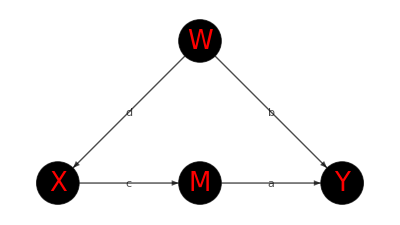

```mathematica
edges = {1->2,2->3,3->4,1->4};
vertices ={1,2,3,4};
vnames = {"W","X","M","Y"};
vweights={Subscript[σ, uW],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={d,c,a,b};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{1,1},{0,0},{1,0},{2,0}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, W],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraph=Graph[{1->2,2->3,3->4,1->4},VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

```mathematica
eweightlookup=Replace[Most@ArrayRules@UpperTriangularize@WeightedAdjacencyMatrix[causalgraph],{x_,y_}:>DirectedEdge[x,y],{2}]
```

{1->2→d,1->4→b,2->3→c,3->4→a}

```mathematica
ParentNodes[graph_,node_]:=VertexInComponent[graph,Replace[node,vlookup],{1}];
ParentEdges[graph_,node_]:=Map[#->Replace[node,vlookup]&,ParentNodes[graph,node]];
NodeStructure[graph_,node_]:={Symbol[node]->Total[MapThread[Replace[#1,eweightlookup]*Symbol[Replace[#2,vlookupname]]&,{ParentEdges[graph,node],ParentNodes[graph,node]}]]+Symbol["u"<>node]};
NodesStructure[graph_,nodes_]:=Flatten[Table[NodeStructure[graph,node],{node,nodes}]];
GraphNodeStructure[graph_]:=Flatten[Table[NodeStructure[graph,node],{node,VertexList[graph]/.vlookupname}]];

NodeVariance[graph_,node_]:=ReplaceAll[{Symbol[node]^2->Total[MapThread[Replace[#1,eweightlookup]*Symbol[Replace[#2,vlookupname]]^2&,{ParentEdges[graph,node],ParentNodes[graph,node]}]]+Symbol["u"<>node]^2},vlookupweight];
GraphNodeVariance[graph_]:=Flatten[Table[NodeVariance[graph,node],{node,VertexList[graph]/.vlookupname}]];

uvarpairs=Permutations[uvars,{2}];
uprodrules=Flatten[{MapThread[#1*#1->#2^2&,{uvars,vweights}],Map[#[[1]]*#[[2]]->0&,uvarpairs]}]

NodeCovariance[graph_,node1_,node2_]:=ReplaceAll[Expand[ReplaceRepeated[Symbol[node1]*Symbol[node2],GraphNodeStructure[graph]]],uprodrules];

NodeCovarianceLinComb[graph_,nodes1_,coeffs1_,nodes2_,coeffs2_]:=
Total[Outer[Times,coeffs1,coeffs2]*Table[NodeCovariance[graph,node1,node2],{node1,nodes1},{node2,nodes2}],2];


NodesCovariance[graph_,nodes_]:=Table[NodeCovariance[graph,node1,node2],{node1,nodes},{node2,nodes}];
NodesCovarianceLinComb[graph_,lincombs_]:=Table[NodeCovarianceLinComb[graph,lincomb1[[1]],lincomb1[[2]],lincomb2[[1]],lincomb2[[2]]],{lincomb1,lincombs},{lincomb2,lincombs}];

RCRemove[a_?MatrixQ,row_?VectorQ,col_?VectorQ]:=Module[{nr,nc,krow,kcol},{nr,nc}=Dimensions[a];
krow=Complement[Range[1,nr],row];
kcol=Complement[Range[1,nc],col];
a[[krow,kcol]]];

CondMeans[graph_,varnodes_,condnodes_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovariance[graph,Join[varnodes,condnodes]];
lA=Length[varnodes];
lB=Length[condnodes];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
Transpose[SigAB].Inverse[SigB].Map[Symbol,condnodes]//Simplify
]

CondMeansLinComb[graph_,varlincombs_,condlincombs_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovarianceLinComb[graph,Join[varlincombs,condlincombs]];
lA=Length[varlincombs];
lB=Length[condlincombs];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
Transpose[SigAB].Inverse[SigB]//Simplify
]

CondVar[graph_,varnodes_,condnodes_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovariance[graph,Join[varnodes,condnodes]];
lA=Length[varnodes];
lB=Length[condnodes];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
SigA-Transpose[SigAB].Inverse[SigB].SigAB//Simplify
]
```

{uW^2→σ_uW^2,uX^2→σ_uX^2,uM^2→σ_uM^2,uY^2→σ_uY^2,uW uX→0,uM uW→0,uW uY→0,uW uX→0,uM uX→0,uX uY→0,uM uW→0,uM uX→0,uM uY→0,uW uY→0,uX uY→0,uM uY→0}

```mathematica
Total[{{1,2},{3,4}}*{{1,2},{3,4}},2]
Outer[Times,{1,2,a},{1,2,b}]//MatrixForm
```

30

(1 | 2 | b
2 | 4 | 2 b
a | 2 a | a b)

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
allstructure=GraphNodeStructure[causalgraph]
allvariances=GraphNodeVariance[causalgraph]

Sig=NodesCovariance[causalgraph,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraph,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraph,{"uX","uM"},{"X","M"}]//MatrixForm
```

{W→uW,X→uX+d W,M→uM+c X,Y→a M+uY+b W}

{σ_W^2→σ_uW^2,σ_X^2→σ_uX^2+d σ_W^2,σ_M^2→σ_uM^2+c σ_X^2,σ_Y^2→a σ_M^2+σ_uY^2+b σ_W^2}

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | d^2 σ_uW^2+σ_uX^2 | c d^2 σ_uW^2+c σ_uX^2
c σ_uX^2 | σ_uM^2 | c d^2 σ_uW^2+c σ_uX^2 | σ_uM^2+c^2 d^2 σ_uW^2+c^2 σ_uX^2)

((X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2)
M-c X)

((d^2 σ_uW^2 σ_uX^2)/(d^2 σ_uW^2+σ_uX^2) | 0
0 | 0)

```mathematica
Sig=NodesCovariance[causalgraph,{"uW","uX","uM","uY"}];
Sig//MatrixForm
lA=2;
lB=2;
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
Sig//CharacteristicPolynomial[#,x]&//Factor
Sig//Det
```

(σ_uW^2 | 0 | 0 | 0
0 | σ_uX^2 | 0 | 0
0 | 0 | σ_uM^2 | 0
0 | 0 | 0 | σ_uY^2)

(x-σ_uM^2) (x-σ_uW^2) (x-σ_uX^2) (x-σ_uY^2)

σ_uM^2 σ_uW^2 σ_uX^2 σ_uY^2

```mathematica
Sig=NodeCovarianceLinComb[causalgraph,{"uW","uX"},{A,B},{"uW","uX"},{C,D}]
```

A C σ_uW^2+B D σ_uX^2

```mathematica
Sig=NodesCovarianceLinComb[causalgraph,{{{"uW","uX"},{A,B}},{{"uW","uX"},{C,D}}}]//MatrixForm
```

(A^2 σ_uW^2+B^2 σ_uX^2 | A C σ_uW^2+B D σ_uX^2
A C σ_uW^2+B D σ_uX^2 | C^2 σ_uW^2+D^2 σ_uX^2)

```mathematica
Sig=NodesCovarianceLinComb[causalgraph,{{{"X"},{1}},{{"uM","uX"},{1,-ϵ/d}}}]//MatrixForm
CondMeansLinComb[causalgraph,{{{"X"},{1}}},{{{"uM","uX"},{1,-ϵ/d}}}]
```

(d^2 σ_uW^2+σ_uX^2 | -(ϵ σ_uX^2)/d
-(ϵ σ_uX^2)/d | σ_uM^2+(ϵ^2 σ_uX^2)/d^2)

{{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)}}

### Biases and Variances for [Gupta], Revisited

We can now perform the same manipulations as before, but much more intelligently. The goal here is to develop an approach which is general enough to be applied out of the box to all other conceivable networks. An intermediate goal is being able to apply it to the “confounded mediator” adjustment to the [Gupta] network.

As a reminder, here are the structural equations and estimators:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

```mathematica
Xa = {M,X};
Ya = {Y};

{â,OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {X};
Yc = {M};

{ĉ}=Estimator[Yc,Xc]
```

{(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X),(M.Y X.M-M.M X.Y)/(M.X X.M-M.M X.X)}

{(X.M)/(X.X)}

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
aerror=â-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→M-c X,uY→0}

0

Similarly for c:

```mathematica
structureEqs={M->c*X+uM};
cerror=ĉ-c//.structureEqs
noisenames={"uM"};
noises=Map[Symbol,noisenames];

condmeans=CondMeans[causalgraph,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
cerrorsimp = cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

-c+(X.(uM+c X))/(X.X)

0

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covestimate=aerror*cerror//.structureEqs//Simplify
covestimatesimp = covestimate/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→M-c X,uY→0}

(-c+(X.(uM+c X))/(X.X)) (-a+(M.(a M+uY+(b (-uX+X))/d) X.X-M.X X.(a M+uY+(b (-uX+X))/d))/(-M.X X.M+M.M X.X))

0

### Biases and Variances for Approximate FDC [Gupta], Revisited

In this case, the structural equations are unchanged, but the estimator for a is simplified.
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

```mathematica
Xa = {M};
Ya = {Y};

{OverHat[approxa]}=Estimator[Ya,Xa]

Xc = {X};
Yc = {M};

{ĉ}=Estimator[Yc,Xc]
```

{(M.Y)/(M.M)}

{(X.M)/(X.X)}

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
aerror=OverHat[approxa]-a//.structureEqs;
```

```mathematica
noisenames={"X","uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
abias=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{X,uX,uM,uY}

{X→(c M (d^2 σ_uW^2+σ_uX^2))/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2)),uX→(c M σ_uX^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2)),uM→(M σ_uM^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2)),uY→0}

(b c d σ_uW^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2))

Similarly for c:

```mathematica
structureEqs={M->c*X+uM};
cerror=ĉ-c//.structureEqs
noisenames={"uM"};
noises=Map[Symbol,noisenames];

condmeans=CondMeans[causalgraph,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
cbias = cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

-c+(X.(uM+c X))/(X.X)

0

To calculate the covariance between a and c, we can take advantage of smoothing over conditional variables X and M, since the term (X.uM)/(X.X) is fixed in this case.

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
covestimate=(aerror-abias)*(cerror-cbias)//.structureEqs//Simplify;
covestimate=covestimate//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
covestimateInside =covestimate/((X.uM)/(X.X))//Simplify;
```

{uX,uM,uY}

(X.uM ((-b M.uX+d M.uY+b M.X)/(d M.M)-(b c d σ_uW^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2))))/(X.X)

```mathematica
covinside = (-b M.uX+d M.uY+b M.X)/(d M.M);
covinsidesimp = covinside/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify;
covestimatesimp=((X.uM)/(X.X))(covinsidesimp-(b c d Subscript[σ, uW]^2)/(Subscript[σ, uM]^2+c^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))
```

(X.uM ((b d M.X σ_uW^2)/(M.M (d^2 σ_uW^2+σ_uX^2))-(b c d σ_uW^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2))))/(X.X)

This is quite an interesting expression. If we only desired the expectation value of the term inside the large braces, we could smooth with conditional variable M and arrive at 0, which is checked below, and expected anyway since we have used the correct bias for estimator a. However, now the outside term comes into play. Since uM is composed of an X part and an M part, and the expectation of the bracketed expression is 0, we can disregard the X part. 

The two types of expectation values to consider are : E[(X.M)^2/(X^2 M^2)], which is hard, and E[(X.M)/M^2], which is easy. If X and M are taken to be independent, the former reduces to E[cos^2 θ] where θ is the angle between X and M.

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22}

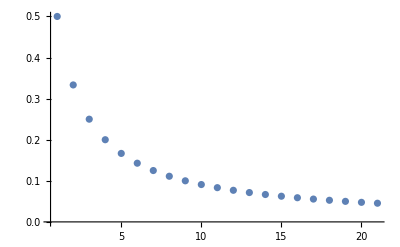

```mathematica
norms=Table[Integrate[Sin[x]^n,{x,0,π}],{n,0,20}];
vals=Table[Integrate[Sin[x]^n*Cos[x]^2,{x,0,π}],{n,0,20}];
normvals=MapThread[#1/#2&,{vals,norms}]
ListPlot[normvals,PlotRange->All]
```

If we impose the true causal dependence M = cX + uM, the expectation value can be reduced geometrically to the following integral, where X is the magnitude of sample vector X (rotated by symmetry to the ẑ direction), Z is the z-component of sample vector uM, and R is the radial component of uM in cylindrical coordinates about z. A constant factor on the front will depend on the dimensionality n of the sample vectors, but by symmetry the integral itself is three-dimensional:

```mathematica
cos2integrand[Cx_,X_,R_,Z_]:=R*X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.stringifySubs;
cos2int=Defer[Integrate[R*X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)],{X,0,∞},{R,0,∞},{Z,0,∞}]]
```

∫_0^∞ ∫_0^∞ ∫_0^∞ (R X^2 (Cx X+Z)^2 Exp[-X^2/(2 σ_X^2)-(R^2+Z^2)/(2 σ_uM^2)])/((Cx X+Z)^2+R^2)ⅆZⅆRⅆX

```mathematica
cos2integrand/.stringifySubs/.{X->X*Subscript[σ, "X"],R->R*Subscript[σ, "uM"],Z->Z*Subscript[σ, "uM"]}//Simplify
```

cos2integrand

```mathematica
fixConsts={Subscript[σ, X]->1,Subscript[σ, uM]->2};
top=Infinity;
CxMax=10;
CxStep=0.5;
normXM=NIntegrate[R^4*X^5 Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.fixConsts,{X,0,top},{R,0,top},{Z,0,top}];
expcos2XM=Table[NIntegrate[R^4 X^5(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.fixConsts,{X,0,top},{R,0,top},{Z,0,top}],{Cx,-1*CxMax,CxMax,CxStep}];
normExpCos2XM=expcos2XM/normXM;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

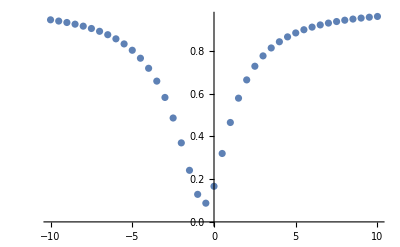

```mathematica
ListPlot[Transpose@{Range[-1*CxMax,CxMax,CxStep],normExpCos2XM},PlotRange->All]
```

```mathematica
Series[(X+Z)^2/((X+Z)^2+R^2),{Z,0,10}]//Simplify
Integrate[Z^n Exp[Z^2/-2],{Z,0,∞}]
```

X^2/(R^2+X^2)+(2 R^2 X Z)/((R^2+X^2)^2)+((R^4-3 R^2 X^2) Z^2)/((R^2+X^2)^3)+(4 R^2 X (-R^2+X^2) Z^3)/((R^2+X^2)^4)-(R^2 (R^4-10 R^2 X^2+5 X^4) Z^4)/((R^2+X^2)^5)+((6 R^6 X-20 R^4 X^3+6 R^2 X^5) Z^5)/((R^2+X^2)^6)+((R^8-21 R^6 X^2+35 R^4 X^4-7 R^2 X^6) Z^6)/((R^2+X^2)^7)+(8 (-R^8 X+7 R^6 X^3-7 R^4 X^5+R^2 X^7) Z^7)/((R^2+X^2)^8)-(R^2 (R^8-36 R^6 X^2+126 R^4 X^4-84 R^2 X^6+9 X^8) Z^8)/((R^2+X^2)^9)+(2 R^2 X (5 R^8-60 R^6 X^2+126 R^4 X^4-60 R^2 X^6+5 X^8) Z^9)/((R^2+X^2)^10)+(R^2 (R^10-55 R^8 X^2+330 R^6 X^4-462 R^4 X^6+165 R^2 X^8-11 X^10) Z^10)/((R^2+X^2)^11)+O[Z]^11

ConditionalExpression[2^(1/2 (-1+n)) Gamma[(1+n)/2], Re[n]>-1]

```mathematica
Simplify[Integrate[R*X^2 Exp[-X^2/2-R^2/2],{Z,0,∞}],Assumptions->{{X,R}∈Reals}]
```

Integrate::idiv: Integral of ⅇ^(-R^2/2-X^2/2) R X^2 does not converge on {0,∞}.

Integrate::idiv: Integral of 1 does not converge on {0,∞}.

ⅇ^(-R^2/2-X^2/2) R X^2 ∫_0^∞ 1ⅆZ

Another direction is to apply the Cauchy-Schwarz Inequality: E[(X.M)^2/(X^2 M^2)] ≤√(E[(X.M)/X^2]E[(X.M)/M^2])= √(F_XM F_MX), establishing an explicit upper bound on the covariance (which is positive by the positivity of both components of (X.M)^2/(X^2 M^2).

```mathematica
noisenames={"X"};
noises=Map[Symbol,noisenames];
condmeanXonM=CondMeans[causalgraph,noisenames,{"M"}][[1]];
noisenames={"M"};
noises=Map[Symbol,noisenames];
condmeanMonX=CondMeans[causalgraph,noisenames,{"X"}][[1]];
CSUpperBound=Sqrt[condmeanMonX*condmeanXonM/(X*M)]//Simplify
```

√((c^2 (d^2 σ_uW^2+σ_uX^2))/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
covestimateterms=covestimatesimp/.stringifySubs/.{uM->M-c*X}//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Expand
covtermslist=List@@covestimateterms;
```

-(b c d M.X σ_uW^2)/(M.M (d^2 σ_uW^2+σ_uX^2))+(b d M.X X.M σ_uW^2)/(M.M X.X (d^2 σ_uW^2+σ_uX^2))+(b c^2 d σ_uW^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2))-(b c d X.M σ_uW^2)/(X.X (σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
covExact=(covtermslist[[1]]/.{X->condmeanXonM}) + covtermslist[[2]]+covtermslist[[3]]+(covtermslist[[4]]/.{M->condmeanMonX})/.stringifySubs//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Expand
```

(b d M.X X.M σ_uW^2)/(M.M X.X (d^2 σ_uW^2+σ_uX^2))-(b c^2 d σ_uW^2)/(σ_uM^2+c^2 (d^2 σ_uW^2+σ_uX^2))

### Biases and Variances for Approximate Approximate FDC [Gupta]

In this case, the structural equations are again unchanged, but the estimator for ac is made directly from X→Y:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

```mathematica
Xac = {X};
Yac = {Y};

{OverHat[approxac]}=Estimator[Yac,Xac]
```

{(X.Y)/(X.X)}

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
acerror=OverHat[approxac]-a*c//.structureEqs
```

-a c+(X.(a M+uY+(b (-uX+X))/d))/(X.X)

```mathematica
noisenames={"M","uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
acbias=acerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{M,uX,uM,uY}

{M→c X,uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→0,uY→0}

(b d σ_uW^2)/(d^2 σ_uW^2+σ_uX^2)

### Biases and Variances for [Gupta] NEW, Revisited

We now adjust the approach by considering u^m to be an instrumental variable

As a reminder, here are the structural equations and estimators:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

Let

```mathematica
Xa = {M,X};
Ya = {Y};

{â,OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {X};
Yc = {M};

{ĉ}=Estimator[Yc,Xc]
```

{(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X),(M.Y X.M-M.M X.Y)/(M.X X.M-M.M X.X)}

{(X.M)/(X.X)}

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
aerror=â-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→M-c X,uY→0}

0

Similarly for c:

```mathematica
structureEqs={M->c*X+uM};
cerror=ĉ-c//.structureEqs
noisenames={"uM"};
noises=Map[Symbol,noisenames];

condmeans=CondMeans[causalgraph,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
cerrorsimp = cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

-c+(X.(uM+c X))/(X.X)

0

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covestimate=aerror*cerror//.structureEqs//Simplify
covestimatesimp = covestimate/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→M-c X,uY→0}

(-c+(X.(uM+c X))/(X.X)) (-a+(M.(a M+uY+(b (-uX+X))/d) X.X-M.X X.(a M+uY+(b (-uX+X))/d))/(-M.X X.M+M.M X.X))

0

### Biases and Variances with Confounded Mediator, Revisited

As a reminder, here are the structural equations and estimators:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

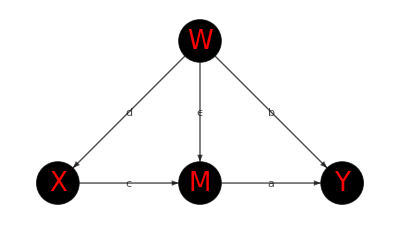

```mathematica
edges = {1->2,2->3,3->4,1->4,1->3};
vertices ={1,2,3,4};
vnames = {"W","X","M","Y"};
vweights={Subscript[σ, uW],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={d,c,a,b,ϵ};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{1,1},{0,0},{1,0},{2,0}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, W],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraphcm=Graph[edges,VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

```mathematica
eweightlookup=Replace[Most@ArrayRules@UpperTriangularize@WeightedAdjacencyMatrix[causalgraphcm],{x_,y_}:>DirectedEdge[x,y],{2}]
```

{1->2→d,1->4→b,1->3→ϵ,2->3→c,3->4→a}

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
allstructure=GraphNodeStructure[causalgraphcm]
allvariances=GraphNodeVariance[causalgraphcm]

Sig=NodesCovariance[causalgraphcm,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraphcm,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraphcm,{"uX","uM"},{"X","M"}]//MatrixForm
```

{W→uW,X→uX+d W,M→uM+c X+W ϵ,Y→a M+uY+b W}

{σ_W^2→σ_uW^2,σ_X^2→σ_uX^2+d σ_W^2,σ_M^2→σ_uM^2+ϵ σ_W^2+c σ_X^2,σ_Y^2→a σ_M^2+σ_uY^2+b σ_W^2}

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | d^2 σ_uW^2+σ_uX^2 | c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2
c σ_uX^2 | σ_uM^2 | c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2 | σ_uM^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2)

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))
(σ_uM^2 (d (d (M-c X)-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

((d^2 σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)) | (d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))
(d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)) | (ϵ^2 σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
CharacteristicPolynomial[Sig,x]//Factor
```

x (x^3-2 x^2 σ_uM^2-d^2 x^2 σ_uW^2-c^2 d^2 x^2 σ_uW^2-2 c d x^2 ϵ σ_uW^2-x^2 ϵ^2 σ_uW^2+2 d^2 x σ_uM^2 σ_uW^2+c^2 d^2 x σ_uM^2 σ_uW^2+2 c d x ϵ σ_uM^2 σ_uW^2+x ϵ^2 σ_uM^2 σ_uW^2-2 x^2 σ_uX^2-c^2 x^2 σ_uX^2+4 x σ_uM^2 σ_uX^2+c^2 x σ_uM^2 σ_uX^2+d^2 x σ_uW^2 σ_uX^2+c^2 d^2 x σ_uW^2 σ_uX^2+2 c d x ϵ σ_uW^2 σ_uX^2+2 x ϵ^2 σ_uW^2 σ_uX^2-2 d^2 σ_uM^2 σ_uW^2 σ_uX^2-c^2 d^2 σ_uM^2 σ_uW^2 σ_uX^2-2 c d ϵ σ_uM^2 σ_uW^2 σ_uX^2-2 ϵ^2 σ_uM^2 σ_uW^2 σ_uX^2)

Extending our causal graph to have a dependency W→M, linearly controlled by ϵ, modifies the structural equations as follows:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

Applying the standard FDC is not technically permitted, because node X no longer blocks all backdoor paths from M to Y; however, since W is unobserved, it cannot be a member of the FDC set. Since the intention is to evaluate error from violating this very assumption, we apply the FDC with {X,M} regardless, and obtain estimators as follows:

m_i = cx_i+ϵ/d(x_i-(u^x)_i)+(u^m)_i
y_i = am_i+b/d(x_i-(u^x)_i)+ϵ/b(m_i-(u^m)_i)+(u^y)_i.

```mathematica
Xa = {M,X};
Ya = {Y};

{OverHat[aplusedivb],OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {X};
Yc = {M};

{OverHat[cplusedivd]}=Estimator[Yc,Xc]
```

{(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X),(M.Y X.M-M.M X.Y)/(M.X X.M-M.M X.X)}

{(X.M)/(X.X)}

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
aerror=OverHat[aplusedivb]-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphcm,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (d (d (M-c X)-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),0}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (d (d (M-c X)-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uY→0}

-a-(a M.X X.M)/(-M.X X.M+M.M X.X)+(a M.M X.X)/(-M.X X.M+M.M X.X)-(b ϵ M.X X.M σ_uW^2 σ_uX^2)/((-M.X X.M+M.M X.X) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))+(b ϵ M.M X.X σ_uW^2 σ_uX^2)/((-M.X X.M+M.M X.X) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

(b ϵ σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))

```mathematica
aerrorsimp/.{b->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
aerrorsimp/.{b->1,d->1,ϵ->0.1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

0.222222

0.0497512

```mathematica
(b ϵ Subscript[σ, uW]^2 Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))-b/ϵ//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

-b/ϵ+(b ϵ σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))

```mathematica
noisenames={"X"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphcm,noisenames,{"M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{X}

{X→(M (d (c d+ϵ) σ_uW^2+c σ_uX^2))/(σ_uM^2+(c d+ϵ)^2 σ_uW^2+c^2 σ_uX^2)}

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Similarly for c:

```mathematica
structureEqs={M->c*X+ϵ*W+uM, W->(X-uX)/d};
cerror=OverHat[cplusedivd]-c//.structureEqs//Expand
noisenames={"uM","uX"};
noises=Map[Symbol,noisenames];

condmeans=CondMeans[causalgraphcm,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
cerror/.condmeanreplace
cerrorsimp = cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

-c+(X.(uM+c X+((-uX+X) ϵ)/d))/(X.X)

-c+(X.(c X+(ϵ (X-(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2)))/d))/(X.X)

(d ϵ σ_uW^2)/(d^2 σ_uW^2+σ_uX^2)

```mathematica
cerrorsimpg = cerrorsimp/.{Subscript[σ, uX]^2->Subscript[σ, uX]^2+g^2 Subscript[σ, uV]^2}
cerrorsimpg/.{d->1,ϵ->1,g->1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uV]^2->1}
```

(d ϵ σ_uW^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

1/3

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covestimate=aerror*cerror//.structureEqs//Simplify
covestimatesimp = covestimate//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify//Expand
```

{uX,uM,uY}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2),uM→M-c X,uY→0}

(-a+(M.(a M+uY+(b (-uX+X))/d) X.X-M.X X.(a M+uY+(b (-uX+X))/d))/(-M.X X.M+M.M X.X)) (-c+(X.(uM+c X+((-uX+X) ϵ)/d))/(X.X))

-(b M.uX X.uM)/(d (-M.X X.M+M.M X.X))+(M.uY X.uM)/(-M.X X.M+M.M X.X)+(b ϵ M.uX X.uX)/(d^2 (-M.X X.M+M.M X.X))-(ϵ M.uY X.uX)/(d (-M.X X.M+M.M X.X))+(b ϵ M.X X.uX)/(d^2 (-M.X X.M+M.M X.X))-(ϵ M.X X.uY)/(d (-M.X X.M+M.M X.X))+(b M.X X.uM X.uX)/(d X.X (-M.X X.M+M.M X.X))-(b ϵ M.X (X.uX)^2)/(d^2 X.X (-M.X X.M+M.M X.X))-(M.X X.uM X.uY)/(X.X (-M.X X.M+M.M X.X))+(ϵ M.X X.uX X.uY)/(d X.X (-M.X X.M+M.M X.X))-(b ϵ M.uX X.X)/(d^2 (-M.X X.M+M.M X.X))+(ϵ M.uY X.X)/(d (-M.X X.M+M.M X.X))

```mathematica
Xa = {R,X};
Ya = {y};
{â,OverHat[bdivd]}=Estimator[Ya,Xa]
```

{(R.y X.X-R.X X.y)/(-R.X X.R+R.R X.X),(R.y X.R-R.R X.y)/(R.X X.R-R.R X.X)}

```mathematica
covRX = -c*X.uX + (M.X X.uX)/(X.X);
noisenames={"M"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphcm,noisenames,{"X","uX"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covRXsimp=covRX/.condmeanreplace
covRXsimp2 = covRXsimp//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify//Expand

noisenames={"uX"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphcm,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covRXsimp3=covRXsimp2/.condmeanreplace
covRXsimp4 = covRXsimp3//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify//Expand
```

{M}

{M→(c d X-uX ϵ+X ϵ)/d}

-c X.uX+(X.uX (c d X-uX ϵ+X ϵ)/d.X)/(X.X)

(ϵ X.uX)/d-(ϵ uX.X X.uX)/(d X.X)

{uX}

{uX→(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2)}

(ϵ X.(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2))/d-(ϵ X.(X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2) (X σ_uX^2)/(d^2 σ_uW^2+σ_uX^2).X)/(d X.X)

(d ϵ X.X σ_uW^2 σ_uX^2)/((d^2 σ_uW^2+σ_uX^2)^2)

### Confounded Mediator, Instrumental Variable Approach

Once again we recall the confounded-mediator structure equations:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

In a standard instrumental variable (IV) approach, an observable variable V is identified which independently causes M with coefficient a: V→M, where the dependence coefficient a: M→Y is to be estimated. Assuming that V is independent of any other causes of M or Y, it can be called an instrumental variable, and it is possible to define the sequence of estimators:
OverHat[ca]=(V.Y)/(V.V)
ĉ=(V.M)/(V.V)
and finally
â=OverHat[ca]/(ĉ).
â is unbiased, even if some confounding variable W directly influences both M and Y.

Our approach to the confounded-mediator graph is to use u^M as an IV for a: M→Y. Of course, u^M is not itself observable, but it can be unbiasedly estimated as the residual of M on X. That is,
u^M = M-(X.M)/(X.X)X = M - ĉ X.
This expression is exact if ϵ=0, in which case the IV approach gives an unbiased estimator for a which is an alternative to the FDC. However, for nonzero ϵ, the residual of M on X is found:
m_i = cx_i+ϵ/d(x_i-(u^x)_i)+(u^m)_i = (c+ϵ/d)x_i+(u^m)_i-ϵ/d(u^x)_i,
(u^m)_i-ϵ/d(u^x)_i = M-(X.M)/(X.X)X

The relevant combined structure equations for these estimators are:
m_i = cx_i+ϵ/d(x_i-(u^x)_i)+(u^m)_i
y_i = a(c+ϵ/d)x_i+bw_i+a((u^m)_i-ϵ/d(u^x)_i)+(u^y)_i

```mathematica
Xa = {M,X};
Ya = {Y};

{OverHat[aplusedivb],OverHat[bdivd]}=Estimator[Ya,Xa]

Xc = {X};
Yc = {M};

{OverHat[cplusedivd]}=Estimator[Yc,Xc]
OverHat[residual] = X-OverHat[cplusedivd] M

{â}=Estimator[{Y},{ϵ/d M+uM-ϵ/d uX}]
{OverHat[apre]}=Estimator[{M},{ϵ/d M+uM-ϵ/d uX}]
{â}=Estimator[{Y},{uM-ϵ/d uX}]
{OverHat[apre]}=Estimator[{M},{uM-ϵ/d uX}]
```

{(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X),(M.Y X.M-M.M X.Y)/(M.X X.M-M.M X.X)}

{(X.M)/(X.X)}

X-(M X.M)/(X.X)

{((d uM+M ϵ-uX ϵ)/d.Y)/((d uM+M ϵ-uX ϵ)/d.(d uM+M ϵ-uX ϵ)/d)}

{((d uM+M ϵ-uX ϵ)/d.M)/((d uM+M ϵ-uX ϵ)/d.(d uM+M ϵ-uX ϵ)/d)}

{((uM-(uX ϵ)/d).Y)/((uM-(uX ϵ)/d).(uM-(uX ϵ)/d))}

{((uM-(uX ϵ)/d).M)/((uM-(uX ϵ)/d).(uM-(uX ϵ)/d))}

```mathematica
structureEqs={Y->a*(uM-(ϵ uX)/d)+a(c+ϵ/d)X+b*W+uY};
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
aerrorIV=â-a//.{(d uM+M ϵ-uX ϵ)/d->eMX,uM-(uX ϵ)/d->eMX2}
apreerrorIV=OverHat[apre]-1//.{(d uM+M ϵ-uX ϵ)/d->eMX,uM-(uX ϵ)/d->eMX2}
```

-a+(eMX2.Y)/(eMX2.eMX2)

-1+(eMX2.M)/(eMX2.eMX2)

```mathematica
noisenames={"uX","X","M","uY","Y"};
noises=Map[Symbol,noisenames]

condmeans=CondMeansLinComb[causalgraphcm,{{{"uX"},{1}},{{"X"},{1}},{{"M"},{1}},{{"uY"},{1}},{{"Y"},{1}}},{{{"M","uM","uX"},{0,1,-ϵ/d}}}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimpIV=aerrorIV/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
apreerrorsimpIV=apreerrorIV/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,X,M,uY,Y}

{{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},{(d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},{0},{(a d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)}}

{uX→{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},X→{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},M→{(d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)},uY→{0},Y→{(a d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)}}

-a+(eMX2.{(a d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)})/(eMX2.eMX2)

-1+(eMX2.{(d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)})/(eMX2.eMX2)

```mathematica
numerics={a->1,b->1,c->-2,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1};
aerrorsimpIV=(a d (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2))/(d^2 Subscript[σ, uM]^2+ϵ^2 Subscript[σ, uX]^2)-a;
apreerrorsimpIV=(d (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2))/(d^2 Subscript[σ, uM]^2+ϵ^2 Subscript[σ, uX]^2)-1;
aerrorsimpIV/.numerics
apreerrorsimpIV/.numerics
```

0.6

0.6

```mathematica
aerrorsimp
aerrorsimp/.numerics
```

ComplexInfinity

ComplexInfinity

```mathematica
aerrorsimp=-((c d+ϵ) ϵ Subscript[σ, uX]^2)/(d^2 Subscript[σ, uM]^2+ϵ^2 Subscript[σ, uX]^2)*a
aerrorsimp=(a d (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2))/(d^2 Subscript[σ, uM]^2+ϵ^2 Subscript[σ, uX]^2)-a
```

-(a ϵ (c d+ϵ) σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)

-a+(a d (d σ_uM^2-c ϵ σ_uX^2))/(d^2 σ_uM^2+ϵ^2 σ_uX^2)

```mathematica
aerrorsimp/.{a->1,b->1,c->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

-0.6

```mathematica
Y = a(uM - e/d uX)+(uY +bW)+(ca+ea/d)X
E[(Y.(uM - e/d uX))/((uM - e/d uX).(uM - e/d uX))] = a + a(c+e/d)E[(X.(uM - e/d uX))/((uM - e/d uX).(uM - e/d uX))]
```

bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X

Set::write: Tag ⅇ in ⅇ[((bW+a (uM-Power[«2»] e uX)+uY+(ca+Power[«2»] ea) X).(uM-(e uX)/d))/((uM-(e uX)/d).(uM-(e uX)/d))] is Protected.

a+a (c+e/d) ⅇ[(X.(uM-(e uX)/d))/((uM-(e uX)/d).(uM-(e uX)/d))]

```mathematica
CondMeansLinComb[causalgraph,{{{"X"},{1}}},{{{"uM","uX"},{1,-ϵ/d}}}]
```

{{-(d ϵ σ_uX^2)/(d^2 σ_uM^2+ϵ^2 σ_uX^2)}}

### Instrumental Variables for Chains of Confounded Mediators

The following case is well known as a simple success of IVs.
w_i = (u^w)_i,
x_i =(u^x)_i,
m_i = cx_i+dw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

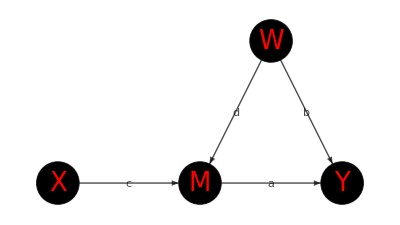

```mathematica
edges = {1->2,2->3,4->2,4->3};
vertices ={1,2,3,4};
vnames = {"X","M","Y","W"};
vweights={Subscript[σ, uW],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={c,a,d,b};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{0,0},{1,0},{2,0},{1.5,1}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, W],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraphiv=Graph[edges,VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

```mathematica
eweightlookup=Replace[Most@ArrayRules@WeightedAdjacencyMatrix[causalgraphiv],{x_,y_}:>DirectedEdge[x,y],{2}]
```

{1->2→c,2->3→a,4->2→d,4->3→b}

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
allstructure=GraphNodeStructure[causalgraphiv]
allvariances=GraphNodeVariance[causalgraphiv]

Sig=NodesCovariance[causalgraphiv,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraphiv,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraphiv,{"uX","uM"},{"X","M"}]//MatrixForm
```

{X→uX,M→uM+d W+c X,bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X→a M+uY+b W,W→uW}

{σ_W^2→σ_uW^2,σ_X^2→σ_uX^2+c σ_W^2+d σ_(bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X)^2,σ_M^2→σ_uM^2+a σ_X^2+b σ_(bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X)^2,σ_(bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X)^2→σ_uY^2}

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
c σ_uX^2 | σ_uM^2 | c σ_uX^2 | σ_uM^2+d^2 σ_uW^2+c^2 σ_uX^2)

(X
((M-c X) σ_uM^2)/(σ_uM^2+d^2 σ_uW^2))

(0 | 0
0 | (d^2 σ_uM^2 σ_uW^2)/(σ_uM^2+d^2 σ_uW^2))

```mathematica
CharacteristicPolynomial[Sig,x]//Factor
```

x (x^3-2 x^2 σ_uM^2-d^2 x^2 σ_uW^2+d^2 x σ_uM^2 σ_uW^2-2 x^2 σ_uX^2-c^2 x^2 σ_uX^2+4 x σ_uM^2 σ_uX^2+c^2 x σ_uM^2 σ_uX^2+2 d^2 x σ_uW^2 σ_uX^2-2 d^2 σ_uM^2 σ_uW^2 σ_uX^2)

Extending our causal graph to have a dependency W→M, linearly controlled by ϵ, modifies the structural equations as follows:
w_i = (u^w)_i,
x_i = dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

Applying the standard FDC is not technically permitted, because node X no longer blocks all backdoor paths from M to Y; however, since W is unobserved, it cannot be a member of the FDC set. Since the intention is to evaluate error from violating this very assumption, we apply the FDC with {X,M} regardless, and obtain estimators as follows:

m_i = cx_i+ϵ/d(x_i-(u^x)_i)+(u^m)_i
y_i = am_i+b/d(x_i-(u^x)_i)+ϵ/b(m_i-(u^m)_i)+(u^y)_i.

```mathematica
Xa = {X};
Ya = {M};

{ĉ}=Estimator[Ya,Xa]

Xc = {X};
Yc = {Y};

{OverHat[ca]}=Estimator[Yc,Xc]

OverHat[aIV]=OverHat[ca]/ĉ
```

{(X.M)/(X.X)}

{(X.(bW+a (uM-(e uX)/d)+uY+ca X+(ea X)/d))/(X.X)}

(X.(bW+a (uM-(e uX)/d)+uY+ca X+(ea X)/d))/(X.M)

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(M-uM)/d};
aerror=OverHat[aIV]-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→X,uM→((M-c X) σ_uM^2)/(σ_uM^2+d^2 σ_uW^2),uY→0}

-a+(X.(bW+ca X+(ea X)/d+a (-(e X)/d+((M-c X) σ_uM^2)/(σ_uM^2+d^2 σ_uW^2))))/(X.M)

```mathematica
aIVcorr=(OverHat[ca]-c*a)(ĉ-c)//Expand//.structureEqs;
noisenames={"uX","uM","uY","M","Y"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aIVcorrsimp=aIVcorr/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY,M,bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X}

{uX→X,uM→0,uY→0,M→c X,bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X→a c X}

0

```mathematica
aerrorsimp/.{b->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
aerrorsimp/.{b->1,d->1,ϵ->0.1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

-a+(X.(bW+ca X+ea X+a (-e X+1/2 (M-c X))))/(X.M)

-a+(X.(bW+ca X+ea X+a (-e X+1/2 (M-c X))))/(X.M)

```mathematica
(b ϵ Subscript[σ, uW]^2 Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))-b/ϵ//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

-b/ϵ+(b ϵ σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))

```mathematica
noisenames={"X"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphcm,noisenames,{"M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{X}

{X→(c M σ_uX^2)/(σ_uM^2+c^2 σ_uX^2)}

1/(d M.M (σ_uM^2+c^2 σ_uX^2))(a d M.uM σ_uM^2-a M.(e uX) σ_uM^2+d M.uY σ_uM^2+c d M.(ca M) σ_uX^2+c M.(ea M) σ_uX^2+a c^2 d M.uM σ_uX^2-a c^2 M.(e uX) σ_uX^2+c^2 d M.uY σ_uX^2+d M.bW (σ_uM^2+c^2 σ_uX^2)-a d M.M (σ_uM^2+c^2 σ_uX^2))

Similarly for c:

```mathematica
structureEqs={M->c*X+ϵ*W+uM, W->(X-uX)/d};
cerror=OverHat[cplusedivd]-c//.structureEqs//Expand
noisenames={"uM","uX"};
noises=Map[Symbol,noisenames];

condmeans=CondMeans[causalgraphcm,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}];
cerror/.condmeanreplace
cerrorsimp = cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

-c+(X.(uM+c X+((-uX+X) ϵ)/d))/(X.X)

-c+(X.(c X))/(X.X)

0

```mathematica
cerrorsimp/.{d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1}
```

0

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(X-uX)/d};
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraph,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
covestimate=aerror*cerror//.structureEqs//Simplify
covestimatesimp = covestimate//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify//Expand
```

{uX,uM,uY}

{uX→X,uM→M-c X,uY→0}

(-a+(X.(bW+a uM-(a e uX)/d+uY+ca X+(ea X)/d))/(X.M)) (-c+(X.(uM+c X+((-uX+X) ϵ)/d))/(X.X))

-(a ϵ)/d+(ϵ X.bW)/(d X.M)+(a ϵ X.uM)/(d X.M)-(a ϵ X.(e uX))/(d^2 X.M)+(ϵ X.uY)/(d X.M)-(a X.uM)/(X.X)+(X.bW X.uM)/(X.M X.X)+(a (X.uM)^2)/(X.M X.X)+(a ϵ X.uX)/(d X.X)-(ϵ X.bW X.uX)/(d X.M X.X)-(a ϵ X.uM X.uX)/(d X.M X.X)-(a X.uM X.(e uX))/(d X.M X.X)+(a ϵ X.uX X.(e uX))/(d^2 X.M X.X)+(X.uM X.uY)/(X.M X.X)-(ϵ X.uX X.uY)/(d X.M X.X)+(ϵ X.(ca X))/(d X.M)+(X.uM X.(ca X))/(X.M X.X)-(ϵ X.uX X.(ca X))/(d X.M X.X)+(ϵ X.(ea X))/(d^2 X.M)+(X.uM X.(ea X))/(d X.M X.X)-(ϵ X.uX X.(ea X))/(d^2 X.M X.X)

### Instrumental Variables for Chains of Confounded Mediators, New Estimators

We now consider the confounded mediator graph with an added instrument V prior to X.
w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

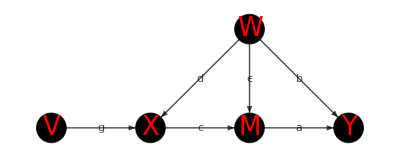

```mathematica
edges = {1->2,2->3,3->4,5->2,5->3,5->4};
vertices ={1,2,3,4,5};
vnames = {"V","X","M","Y","W"};
vweights={Subscript[σ, uV],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY],Subscript[σ, uW]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={g,c,a,d,ϵ,b};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{0,0},{1,0},{2,0},{3,0},{2,1}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, V],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y],Subscript[σ, W]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraphiv2=Graph[edges,VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

```mathematica
eweightlookup=Replace[Most@ArrayRules@WeightedAdjacencyMatrix[causalgraphiv2],{x_,y_}:>DirectedEdge[x,y],{2}]
uvarpairs=Permutations[uvars,{2}];
uprodrules=Flatten[{MapThread[#1*#1->#2^2&,{uvars,vweights}],Map[#[[1]]*#[[2]]->0&,uvarpairs]}]
```

{1->2→g,2->3→c,3->4→a,5->2→d,5->3→ϵ,5->4→b}

{uV^2→σ_uV^2,uX^2→σ_uX^2,uM^2→σ_uM^2,uY^2→σ_uY^2,uW^2→σ_uW^2,uV uX→0,uM uV→0,uV uY→0,uV uW→0,uV uX→0,uM uX→0,uX uY→0,uW uX→0,uM uV→0,uM uX→0,uM uY→0,uM uW→0,uV uY→0,uX uY→0,uM uY→0,uW uY→0,uV uW→0,uW uX→0,uM uW→0,uW uY→0}

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
NodeCovariance[graph_,node1_,node2_]:=ReplaceAll[Expand[ReplaceRepeated[Symbol[node1]*Symbol[node2],GraphNodeStructure[graph]]],uprodrules];
uV
uX
uW
uM
uW
```

uV

uX

uW

uM

uW

```mathematica
allstructure=GraphNodeStructure[causalgraphiv2]
allvariances=GraphNodeVariance[causalgraphiv2]
NodeCovariance[causalgraphiv2,"uX","X"]
Sig=NodesCovariance[causalgraphiv2,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraphiv2,{"uX"},{"X","M"}]//MatrixForm
CondMeans[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X→a M+uY+b W,W→uW}

{σ_V^2→σ_uV^2,σ_X^2→σ_uX^2+g σ_V^2+d σ_W^2,σ_M^2→σ_uM^2+ϵ σ_W^2+c σ_X^2,σ_(bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X)^2→a σ_M^2+σ_uY^2+b σ_W^2,σ_W^2→σ_uW^2}

σ_uX^2

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2
c σ_uX^2 | σ_uM^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2 | σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2)

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((g^2 ϵ^2 σ_uV^2 σ_uW^2+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2)) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (ϵ^2 σ_uM^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

```mathematica
CharacteristicPolynomial[Sig,x]//Factor
```

x^4-2 x^3 σ_uM^2-g^2 x^3 σ_uV^2-c^2 g^2 x^3 σ_uV^2+2 g^2 x^2 σ_uM^2 σ_uV^2+c^2 g^2 x^2 σ_uM^2 σ_uV^2-d^2 x^3 σ_uW^2-c^2 d^2 x^3 σ_uW^2-2 c d x^3 ϵ σ_uW^2-x^3 ϵ^2 σ_uW^2+2 d^2 x^2 σ_uM^2 σ_uW^2+c^2 d^2 x^2 σ_uM^2 σ_uW^2+2 c d x^2 ϵ σ_uM^2 σ_uW^2+x^2 ϵ^2 σ_uM^2 σ_uW^2+g^2 x^2 ϵ^2 σ_uV^2 σ_uW^2-g^2 x ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2-2 x^3 σ_uX^2-c^2 x^3 σ_uX^2+4 x^2 σ_uM^2 σ_uX^2+c^2 x^2 σ_uM^2 σ_uX^2+g^2 x^2 σ_uV^2 σ_uX^2+c^2 g^2 x^2 σ_uV^2 σ_uX^2-2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2-c^2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2+d^2 x^2 σ_uW^2 σ_uX^2+c^2 d^2 x^2 σ_uW^2 σ_uX^2+2 c d x^2 ϵ σ_uW^2 σ_uX^2+2 x^2 ϵ^2 σ_uW^2 σ_uX^2-2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-c^2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-2 c d x ϵ σ_uM^2 σ_uW^2 σ_uX^2-2 x ϵ^2 σ_uM^2 σ_uW^2 σ_uX^2-g^2 x ϵ^2 σ_uV^2 σ_uW^2 σ_uX^2+g^2 ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2 σ_uX^2

We will now seek to construct an estimator with improved bias or variance over the standard IV estimators on causal effects a and ca.

w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

ResXV = X - gV = dW + uX
ResMX = M - cX = eW + uM

E_samples[ϵ/d]

Sample i = {(W),V,X,M,Y}


E[X - gV = dW + uX]
E[X] - g E[V] = d E[W] = 0

Unbiased
g
c
dW_i+uX_i
eW_i+uM_i

c+e/d (small bias)


c
eW_i+uM_i
W->X uniquely:   uW = (X-ux)/d

X = dW + uX
M = eW + cX + uM

e .dinv(dw) - e.dinv(dw + ux)
e(W) - e.dinv(dw + uX)
bias ~= E[dW.uX] + Ew[dW^2]




Key residual: Res’ = uM - e/d uX -  α*Cov(X,uM-e/d uX)*X/σ_X,    α ∈ [0,1]
such that Cov(X,Res’) = 0
but Cov(W,Cov(X,uM-e/d uX)*X/σ_X) != 0


V(Res) = σ_uM^2+ϵ^2/d^2 σ_uX^2 =~ 2
Cov(X,Res) =  -ϵ/d σ_uX^2 =~ -1
-- Need to check next order of these i.e. with V->X->M pathway

* Key result: Take res1 = M-((M.X)/(X.X))X as a vector-valued estimator
Then, Cov(X,res1) = E[M.X - M.X] = 0
but Cov(W,res1) = E[W.M - (M.X W.X)/(X.X)] = eE[W.W] - eE[(W.X W.X)/(X.X)] - E[(uM.X W.X)/(X.X)] != 0

This is counter to our intuition about uM - e/d uX, since:
Cov(uM - e/d uX, X) != 0
Cov(uM - e/d uX, W)  = 0

What about res2?

We have (biased) knowledge of OverHat[ϵ/d]
σ_uM^2= V(Res) + OverHat[ϵ/d]Cov(X,Res)
σ_uX^2= - Cov(X,Res)/(OverHat[ϵ/d])
--Can we re-insert samples from learned uM, uX variances to decrease bias?








Using E[A/B] = E[A]/E[B](1-cov[A,B]/(E[A]E[B})+V[B]/E[B]^2),
we have E[A/B] - E[A]/E[B] = (V[B]E[A])/E[B]^3-cov[A,B]/(E[B})^2

Empirically, we see E[(|E|)/(|D|)]=E[|E|]/E[|D|]=√[1/2+(e/d)^2] 
independent of a, b, c, absolute magnitude of e and d, noises,
but NOT g


ResMV-OverHat[edivd]*ResXV = um - e/d ux


1) Check regressing Y on residual (um- e/d ux) AND x
2) Check E[e/d] vs E[e]/E[d] vs E[mag(e)/mag(d)] vs. E[c+e/d] - E[c]
3) Try all e/d estimators with improved (um- e/d ux) instrument for a.


4) Monotonic decrease in e/d, consider even setting e/d constant=K throughout a run and just estimating initial confounding d and K
5) Are there two types of confounders, monotonic and catastrophic?
6)

```mathematica
OverHat[csimp]=(M.X)/(X.X)//Simplify
structureEqs={M->c*X+ϵ*W+uM,W->(X-uX-g*uV)/d};
cerror=OverHat[csimp]-c//.structureEqs//Simplify
noisenames={"uX","uM","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
cerrorsimp=cerror/.condmeanreplace
cerrorsimp=cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(M.X)/(X.X)

-c+((uM+c X-((g uV+uX-X) ϵ)/d).X)/(X.X)

{uX,uM,uV}

{(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),0,(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

{uX→(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),uM→0,uV→(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

-c+((c X-(ϵ (-X+(g^2 X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)+(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))/d).X)/(X.X)

(d ϵ σ_uW^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
{ĉ}=Estimator[{M},{X}];
ResMXSimp=M-ĉ X//Simplify;

{ĝ}=Estimator[{X},{V}];
ResXV=X-ĝ V//Simplify;

{OverHat[gc]}=Estimator[{M},{V}];
ResMV=M-OverHat[gc] V//Simplify;

OverHat[cIV]=OverHat[gc]/ĝ;
ResMX=M-OverHat[cIV] X//Simplify;
```

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//Simplify
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-(X X.M)/(X.X)).Y)/((M-(X X.M)/(X.X)).M)

1/(d ((X.M)^2-M.M X.X))(a d (X.M)^2-(a d M.M-b M.uX+d M.uY-b g M.V+b M.X) X.X+X.M (-b X.uX+d X.uY-b g X.V+b X.X))

OverHat[arem]

OverHat[arem]

1

```mathematica
OverHat[asimp]=(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aerror=OverHat[asimp]-a//.structureEqs//Simplify
```

(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)

-a+(-M.X X.(a M+uY-(b (g uV+uX-X))/d)+M.(a M+uY-(b (g uV+uX-X))/d) X.X)/(-M.X X.M+M.M X.X)

```mathematica
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+1/(-M.X X.M+M.M X.X)(M.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d) X.X-M.X X.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d))

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
aerrorsimp/.{b->1,g->0,Subscript[σ, uW]^2->1,Subscript[σ, uV]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1,Subscript[σ, uY]^2->1}
```

ϵ/(1+d^2+ϵ^2)

```mathematica
OverHat[anum]=M.Y X.X-M.X X.Y//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
anumerror=OverHat[anum]//.structureEqs//Simplify
anumerror=TensorExpand[anumerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
anumerror=anumerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.Y X.X-M.X X.Y

-(g uV+d uW+uX).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ)) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ))

ϵ (b+a ϵ) uW.uW (g^2 uV.uV+uX.uX)+a uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ (b+a ϵ) σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+a σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
OverHat[adenom]=+M.M X.X-M.X X.M//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
adenomerror=OverHat[adenom]//.structureEqs//Simplify
adenomerror=TensorExpand[adenomerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
adenomerror=adenomerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

-M.X X.M+M.M X.X

-(g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)

ϵ^2 uW.uW (g^2 uV.uV+uX.uX)+uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
anumerror/adenomerror - a //Simplify
```

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
{OverHat[cplusedivd]}=Estimator[{M},{X}]
OverHat[edivd]=OverHat[cplusedivd] - OverHat[cIV]

ResNewMXsubed=ResMV-OverHat[edivd]*ResXV//Collect[#,{X,M,V}]&

regress M on V
ResNewMXold=ResMV-(ϵ/d)*ResXV//Collect[#,{X,M,V}]&
regress M on X
ResNewMX=ResMX-(ϵ/d)*ResXV//Collect[#,{X,M,V}]&

(eW + uM) - ϵ/d(dW + uX) = residual


RemNewMX = M - (c+ϵ/d)*X;
eW + uM = remainder
```

{(X.M)/(X.X)}

-(V.M)/(V.X)+(X.M)/(X.X)

M+X ((V.M)/(V.X)-(X.M)/(X.X))+V (-(2 V.M)/(V.V)+(V.X X.M)/(V.V X.X))

M on regress V

M-(X ϵ)/d+V (-(V.M)/(V.V)+(ϵ V.X)/(d V.V))

M on regress X

M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)

Set::write: Tag Plus in (eW+uM)-((dW+uX) ϵ)/d is Protected.

residual

Set::write: Tag Plus in eW+uM is Protected.

remainder

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-X (c+ϵ/d)).Y)/((M-X (c+ϵ/d)).M)

(a d^2 M.M-b d M.uX+d^2 M.uY-b d g M.V+b d M.X-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY+b c d g X.V+b g ϵ X.V-b c d X.X-b ϵ X.X)/(d (d M.M-(c d+ϵ) X.M))

(a d^2 M.M-b d M.uX+d^2 M.uY-b d g V.M+b c d g V.X+b g ϵ V.X+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)/(d (d M.M-(c d+ϵ) X.M))

a d^2 M.M-b d M.uX+d^2 M.uY-b d g V.M+b c d g V.X+b g ϵ V.X+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X

d^2 M.M-c d^2 X.M-d ϵ X.M

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
Numarem=Numerator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomarem=Denominator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-X (c+ϵ/d)).Y)/((M-X (c+ϵ/d)).M)

M.Y-((c d+ϵ) X.Y)/d

M.M-((c d+ϵ) X.M)/d

```mathematica
OverHat[arem]=Numarem/Denomarem//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aremerror=OverHat[arem]-a//.structureEqs//Simplify
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aremerrorsimp=aremerror/.condmeanreplace
```

(d M.Y-(c d+ϵ) X.Y)/(d M.M-(c d+ϵ) X.M)

-a+(d M.(a M+uY-(b (g uV+uX-X))/d)-(c d+ϵ) X.(a M+uY-(b (g uV+uX-X))/d))/(d M.M-(c d+ϵ) X.M)

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+1/(d M.M-(c d+ϵ) X.M)(d M.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d)-(c d+ϵ) X.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d))

```mathematica
-b/d 1/(d M.M-(c d+ϵ) X.M)(d M.((-X+(g^2 Subscript[σ, uV]^2 (X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2))/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))))-(c d+ϵ) X.( (-X+(g^2 Subscript[σ, uV]^2 (X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2))/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))))//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(b σ_uW^2 (-ϵ (-d M.M+(c d+ϵ) X.M) (g^2 σ_uV^2+σ_uX^2)+d M.X (d σ_uM^2-c ϵ (g^2 σ_uV^2+σ_uX^2))+(c d+ϵ) X.X (-d σ_uM^2+c ϵ (g^2 σ_uV^2+σ_uX^2))))/((d M.M-(c d+ϵ) X.M) (ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

```mathematica
b Subscript[σ, uW]^2 (-ϵ (-d M.M+(c d+ϵ) X.M) (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+d M.X (d Subscript[σ, uM]^2-c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2))+(c d+ϵ) X.X (-d Subscript[σ, uM]^2+c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)))/((d M.M-(c d+ϵ) X.M) (ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))/.{X.M->M.X,g->0}//Simplify
```

(b σ_uW^2 (d ϵ M.M σ_uX^2+(c d+ϵ) X.X (-d σ_uM^2+c ϵ σ_uX^2)+M.X (d^2 σ_uM^2-ϵ (2 c d+ϵ) σ_uX^2)))/((d M.M-(c d+ϵ) M.X) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
OverHat[remVar]=RemNewMX.RemNewMX//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[remVar]=OverHat[remVar]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[remVar]=OverHat[remVar]//.{M->c*X+uM+e*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[remVar]=TensorExpand[OverHat[remVar],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[remVar]=OverHat[remVar]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.M+((c d+ϵ) (-d M.X-d X.M+(c d+ϵ) X.X))/d^2

M.M+((c d+ϵ) (-2 d X.M+(c d+ϵ) X.X))/d^2

1/d^2(c d+ϵ) ((c d+ϵ) (g uV+d uW+uX).(g uV+d uW+uX)-2 d (g uV+d uW+uX).(uM+e uW+c (g uV+d uW+uX)))+(uM+e uW+c (g uV+d uW+uX)).(uM+e uW+c (g uV+d uW+uX))

uM.uM+(g^2 ϵ^2 uV.uV)/d^2+e^2 uW.uW-2 e ϵ uW.uW+ϵ^2 uW.uW+(ϵ^2 uX.uX)/d^2

σ_uM^2+(g^2 ϵ^2 σ_uV^2)/d^2+e^2 σ_uW^2-2 e ϵ σ_uW^2+ϵ^2 σ_uW^2+(ϵ^2 σ_uX^2)/d^2

```mathematica
OverHat[aremDen]=RemNewMX.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremDen]=TensorExpand[OverHat[aremDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.M-((c d+ϵ) X.M)/d

M.M-((c d+ϵ) X.M)/d

-((c d+ϵ) (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ))/d+(uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)

uM.uM-(c ϵ (g^2 uV.uV+uX.uX))/d

σ_uM^2-(c ϵ (g^2 σ_uV^2+σ_uX^2))/d

```mathematica
OverHat[aremNum]=RemNewMX.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremNum]=TensorExpand[OverHat[aremNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

1/d^2(a d^2 M.M-b d g M.uV-b d M.uX+d^2 M.uY+b d M.X-a c d^2 X.M-a d ϵ X.M+b c d g X.uV+b g ϵ X.uV+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)

1/d^2(a d^2 M.M-b d g M.uV-b d M.uX+d^2 M.uY+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d g X.uV+b g ϵ X.uV+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)

-1/d^2(-b g (c d+ϵ) (g uV+d uW+uX).uV-b (c d+ϵ) (g uV+d uW+uX).uX+b c d (g uV+d uW+uX).(g uV+d uW+uX)+b ϵ (g uV+d uW+uX).(g uV+d uW+uX)+c d^2 (g uV+d uW+uX).uY+d ϵ (g uV+d uW+uX).uY-b d (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+a c d^2 (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+a d ϵ (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+b d g (uM+c (g uV+d uW+uX)+uW ϵ).uV+b d (uM+c (g uV+d uW+uX)+uW ϵ).uX-d^2 (uM+c (g uV+d uW+uX)+uW ϵ).uY-a d^2 (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ))

a (uM.uM-(c ϵ (g^2 uV.uV+uX.uX))/d)

a (σ_uM^2-(c ϵ (g^2 σ_uV^2+σ_uX^2))/d)

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[ares]=(ResNewMX.Y)/(ResNewMX.M)
Numares=Numerator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomares=Denominator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)).Y)/((M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)).M)

(d M.Y V.V V.X-d V.M V.V X.Y-ϵ V.V V.X X.Y+(V.X)^2 (V ϵ).Y)/d

(d M.M V.V V.X-d V.M V.V X.M-ϵ V.V V.X X.M+(V.X)^2 (V ϵ).M)/d

```mathematica
OverHat[ares]=Numares/Denomares//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
areserror=OverHat[ares]-a//.structureEqs//Simplify
```

(d M.Y V.V V.X-d V.M V.V X.Y-ϵ V.V V.X X.Y+(V.X)^2 (V ϵ).Y)/(d M.M V.V V.X-d V.M V.V X.M-ϵ V.V V.X X.M+(V.X)^2 (V ϵ).M)

-a+(d M.(a M+uY-(b (g uV+uX-X))/d) V.V V.X-d V.M V.V X.(a M+uY-(b (g uV+uX-X))/d)+V.X (-ϵ V.V X.(a M+uY-(b (g uV+uX-X))/d)+V.X (V ϵ).(a M+uY-(b (g uV+uX-X))/d)))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))

```mathematica
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"V","X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
areserrorsimp=areserror/.condmeanreplace
areserrorsimp=areserror*(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&
```

{uX,uM,uY,uW,uV}

{(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (d (d M-c d X+g V ϵ-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d (-g V+X) σ_uM^2+(M-c X) ϵ σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),V}

{uX→(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (d (d M-c d X+g V ϵ-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d (-g V+X) σ_uM^2+(M-c X) ϵ σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uV→V}

-a+(d M.(a M-1/d b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))) V.V V.X-d V.M V.V X.(a M-1/d b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))+V.X (-ϵ V.V X.(a M-1/d b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))+V.X (V ϵ).(a M-1/d b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))

```mathematica
M.M V.V V.X
V.M V.V X.M
V.X V.V X.M
V.X V.X V.M
```

```mathematica
-b/d(d M.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))) V.V V.X-d V.M V.V X.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))+V.X (-ϵ V.V X.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))+V.X (V ϵ).(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(b σ_uW^2 (ϵ^2 V.M (V.X)^2 σ_uX^2+d M.X V.V V.X (d σ_uM^2-c ϵ σ_uX^2)+ϵ (V.X)^3 (d σ_uM^2-c ϵ σ_uX^2)-d V.M V.V (ϵ X.M σ_uX^2+X.X (d σ_uM^2-c ϵ σ_uX^2))+ϵ V.V V.X ((d M.M-ϵ X.M) σ_uX^2+X.X (-d σ_uM^2+c ϵ σ_uX^2))))/((d M.M V.V V.X-ϵ V.V V.X X.M+V.M (ϵ (V.X)^2-d V.V X.M)) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
(b Subscript[σ, uW]^2 (ϵ^2 V.M (V.X)^2 Subscript[σ, uX]^2+d M.X V.V V.X (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2)+ϵ (V.X)^3 (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2)-d V.M V.V (ϵ X.M Subscript[σ, uX]^2+X.X (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2))+ϵ V.V V.X ((d M.M-ϵ X.M) Subscript[σ, uX]^2+X.X (-d Subscript[σ, uM]^2+c ϵ Subscript[σ, uX]^2))))/((d M.M V.V V.X-ϵ V.V V.X X.M+V.M (ϵ (V.X)^2-d V.V X.M)) (ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))//
TraditionalForm
```

(b σ_uW^2 (d V.V M.X V.X (d σ_uM^2-c ϵ σ_uX^2)+V.V ϵ V.X (X.X (c ϵ σ_uX^2-d σ_uM^2)+σ_uX^2 (d M.M-ϵ X.M))-d V.V V.M (X.X (d σ_uM^2-c ϵ σ_uX^2)+ϵ X.M σ_uX^2)+ϵ (V.X)^3 (d σ_uM^2-c ϵ σ_uX^2)+ϵ^2 V.M σ_uX^2 (V.X)^2))/((V.M (ϵ (V.X)^2-d V.V X.M)+d M.M V.V V.X-V.V ϵ X.M V.X) (σ_uM^2 (d^2 σ_uW^2+σ_uX^2)+ϵ^2 σ_uW^2 σ_uX^2))

```mathematica
OverHat[aresDen]=ResNewMXold.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=Collect[OverHat[aresDen],a]
```

1/(d σ_uV^2)((g uV (-c d+ϵ) σ_uV^2).uM+c g (g uV (-c d+ϵ) σ_uV^2).uV+c d (g uV (-c d+ϵ) σ_uV^2).uW+ϵ (g uV (-c d+ϵ) σ_uV^2).uW+c (g uV (-c d+ϵ) σ_uV^2).uX+d σ_uM^2 σ_uV^2+c g^2 (c d-ϵ) σ_uV^4+c σ_uV^2 (d^2 (c d+ϵ) σ_uW^2+(c d-ϵ) σ_uX^2))

(c g^2 (-c d+ϵ) uV.uV+d σ_uM^2+c (g^2 (c d-ϵ) σ_uV^2+d^2 (c d+ϵ) σ_uW^2+(c d-ϵ) σ_uX^2))/d

σ_uM^2+c d (c d+ϵ) σ_uW^2+(c (c d-ϵ) σ_uX^2)/d

σ_uM^2+c d (c d+ϵ) σ_uW^2+(c (c d-ϵ) σ_uX^2)/d

1

1-e/d

{{e→d}}

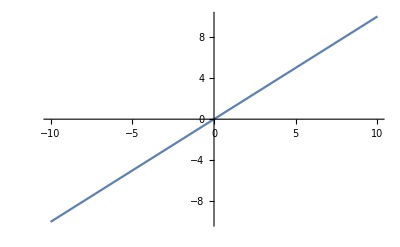

```mathematica
noise=1
aresDenSolve=OverHat[aresDen]/.{c->1,Subscript[σ, uW]^2->noise,Subscript[σ, uX]^2->noise,Subscript[σ, uM]^2->noise}
aresDenSol=Solve[aresDenSolve==0,e]
Plot[e/.aresDenSol[[1]],{d,-10,10}]
```

```mathematica
OverHat[aresNum]=ResNewMXold.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=Collect[OverHat[aresNum],a]
```

1/(d σ_uV^2)(a (g uV (-c d+ϵ) σ_uV^2).uM+a c g (g uV (-c d+ϵ) σ_uV^2).uV+b (g uV (-c d+ϵ) σ_uV^2).uW+a c d (g uV (-c d+ϵ) σ_uV^2).uW+a ϵ (g uV (-c d+ϵ) σ_uV^2).uW+a c (g uV (-c d+ϵ) σ_uV^2).uX+(g uV (-c d+ϵ) σ_uV^2).uY+a d σ_uM^2 σ_uV^2+a c g^2 (c d-ϵ) σ_uV^4+c σ_uV^2 (d^2 (b+a (c d+ϵ)) σ_uW^2+a (c d-ϵ) σ_uX^2))

1/d(a c g^2 (-c d+ϵ) uV.uV+a d σ_uM^2+c (a g^2 (c d-ϵ) σ_uV^2+d^2 (b+a c d+a ϵ) σ_uW^2+a (c d-ϵ) σ_uX^2))

a σ_uM^2+c d (b+a c d+a ϵ) σ_uW^2+(a c (c d-ϵ) σ_uX^2)/d

b c d σ_uW^2+a (σ_uM^2+c^2 d^2 σ_uW^2+c d ϵ σ_uW^2+(c (c d-ϵ) σ_uX^2)/d)

```mathematica
DynamicModule[{a},Column[{Dynamic@Plot[aresBiasNum,{e,0,5},PlotRange->{All,{-3,3}}],Slider[Dynamic@d,{0,5},Label]}]]
```

```mathematica
aresBias=OverHat[(aresNum]/OverHat[aresDen])-a//Simplify
aresBiasNum[d_,e_]=aresBias/.{b->1,c->1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}//Simplify
aresBiasNum[d,e]
aresBiasNum[0.5,1.499]
Manipulate[Plot[aresBiasNum[d,e],{e,0,5},PlotRange->{All,{-3,3}}],{d,0,5,Labeled[Panel@Column[{Slider[##,ImageSize->250],Graphics[{},Axes->{True,False},Ticks->{Subdivide[##&@@#2,5],None},ImageSize->250,PlotRange->{#2,{0,.05}}]},Alignment->Center,Spacings->0],#,Right]&}]
Solve[2 d-e+d^2 (d+e)==0,e]
```

```mathematica
OverHat[slopeMuM]=(ResNewMX.M)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeMuM]=OverHat[slopeMuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeMuM]]//ExpandAll
Denominator[OverHat[slopeMuM]]//ExpandAll
```

(d V.V V.X (d M.M V.V V.X+(V.X)^2 (e V).M-d V.M V.V X.M-e V.V V.X X.M))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3-d M.X (V.V)^2 V.X (d V.M+e V.X)+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

(d V.V V.X (d M.M V.V V.X+(V.X)^2 (e V).M-d V.M V.V X.M-e V.V V.X X.M))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

d^2 M.M (V.V)^2 (V.X)^2+d V.V (V.X)^3 (e V).M-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M

d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X

```mathematica
OverHat[slopeYuM]=(ResNewMX.Y)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeYuM]=OverHat[slopeYuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeYuM]]//ExpandAll
Denominator[OverHat[slopeYuM]]//ExpandAll
```

(d V.V V.X (d M.Y V.V V.X+(V.X)^2 (e V).Y-d V.M V.V X.Y-e V.V V.X X.Y))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3-d M.X (V.V)^2 V.X (d V.M+e V.X)+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

(d V.V V.X (d M.Y V.V V.X+(V.X)^2 (e V).Y-d V.M V.V X.Y-e V.V V.X X.Y))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

d^2 M.Y (V.V)^2 (V.X)^2+d V.V (V.X)^3 (e V).Y-d^2 V.M (V.V)^2 V.X X.Y-d e (V.V)^2 (V.X)^2 X.Y

d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X

```mathematica
OverHat[numslopeYuM]=Numerator[OverHat[slopeYuM]]//Collect[#,{V.X}]&
OverHat[numslopeMuM]=Numerator[OverHat[slopeMuM]]//Collect[#,{V.X}]&
OverHat[aNewIV]=Collect[Simplify[OverHat[numslopeYuM]/-(V.X)],{V.X}]/Collect[Simplify[OverHat[numslopeMuM]/-(V.X)],{V.X}]
```

d V.V (V.X)^3 (e V).Y-d^2 V.M (V.V)^2 V.X X.Y+d V.V (V.X)^2 (d M.Y V.V-e V.V X.Y)

d V.V (V.X)^3 (e V).M-d^2 V.M (V.V)^2 V.X X.M+d V.V (V.X)^2 (d M.M V.V-e V.V X.M)

(-d V.V (V.X)^2 (e V).Y+d^2 V.M (V.V)^2 X.Y+d V.V V.X (-d M.Y V.V+e V.V X.Y))/(-d V.V (V.X)^2 (e V).M+d^2 V.M (V.V)^2 X.M+d V.V V.X (-d M.M V.V+e V.V X.M))

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

Another approach is possible, where instead of retrieving ϵ/dfrom the difference between the IV estimator on C and the backdoor estimator on C+ϵ/d, we extract ϵ/d from the following ratio of residuals:
OverHat[(ϵ/d)]=(m-(m.v)/(x.v)x)/(x-(x.v)/(v.v)v)
We have been a bit notationally irresponsible here, as we are dividing two vectors which are not exactly parallel, due to the noise terms u^m and u^x. On the average they should be parallel, so we take the estimator to be the ratio of magnitudes:
OverHat[(ϵ/d)]=(|m-(m.v)/(x.v)x|)/(|x-(x.v)/(v.v)v|)
More specifically,

```mathematica
OverHat[edivd2]=(ResMX.ResMX)/(ResXV.ResXV)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[edivd2]=OverHat[edivd2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
```

(V.V (M.X V.M V.X-M.M (V.X)^2+V.M (V.X X.M-V.M X.X)))/((V.X)^2 (V.X X.V-V.V X.X))

-(V.V (M.M (V.X)^2+V.M (-2 V.X X.M+V.M X.X)))/((V.X)^4-V.V (V.X)^2 X.X)

```mathematica
ResNewMX2=ResMV-OverHat[edivd2]*ResXV//Simplify//Collect[#,{X,M,V}]&
```

M+X ((M.M V.V (V.X)^2)/((V.X)^4-V.V (V.X)^2 X.X)+(V.M V.V (-2 V.X X.M+V.M X.X))/((V.X)^4-V.V (V.X)^2 X.X))+V (-(V.M)/(V.V)-(M.M (V.X)^3)/((V.X)^4-V.V (V.X)^2 X.X)-(V.M V.X (-2 V.X X.M+V.M X.X))/((V.X)^4-V.V (V.X)^2 X.X))

```mathematica
OverHat[slopeMuM2]=(ResNewMX2.M)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeMuM2]=OverHat[slopeMuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeMuM2]]//ExpandAll;
Denominator[OverHat[slopeMuM2]]//ExpandAll;
```

```mathematica
OverHat[slopeYuM2]=(ResNewMX2.Y)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeYuM2]=OverHat[slopeYuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeYuM2]]//ExpandAll;
Denominator[OverHat[slopeYuM2]]//ExpandAll;
```

```mathematica
OverHat[numslopeYuM2]=Numerator[OverHat[slopeYuM2]]//Collect[#,{V.X}]&
OverHat[numslopeMuM2]=Numerator[OverHat[slopeMuM2]]//Collect[#,{V.X}]&
OverHat[aNewIV2]=Collect[Simplify[OverHat[numslopeYuM2]/(V.X)^2],{V.X}]/Collect[Simplify[OverHat[numslopeMuM2]/(V.X)^2],{V.X}]
```

M.M V.V (V.X)^5 V.Y+(V.X)^6 (-M.Y V.V+V.M V.Y)-(V.M)^2 (V.V)^2 (V.X)^2 X.X X.Y+(V.X)^4 (M.Y (V.V)^2 X.X-V.M V.V V.Y (2 X.M+X.X)-M.M (V.V)^2 X.Y)+V.M V.V (V.X)^3 (V.M V.Y X.X+2 V.V X.M X.Y)

M.M V.M V.V (V.X)^5+((V.M)^2-M.M V.V) (V.X)^6-(V.M)^2 (V.V)^2 (V.X)^2 X.M X.X+(V.X)^3 (2 V.M (V.V)^2 (X.M)^2+(V.M)^3 V.V X.X)+(V.X)^4 (M.M (V.V)^2 (-X.M+X.X)-(V.M)^2 V.V (2 X.M+X.X))

(M.M V.V (V.X)^3 V.Y+(V.X)^4 (-M.Y V.V+V.M V.Y)-(V.M)^2 (V.V)^2 X.X X.Y+V.M V.V V.X (V.M V.Y X.X+2 V.V X.M X.Y)+V.V (V.X)^2 (-V.M V.Y (2 X.M+X.X)+V.V (M.Y X.X-M.M X.Y)))/(M.M V.M V.V (V.X)^3+((V.M)^2-M.M V.V) (V.X)^4-(V.M)^2 (V.V)^2 X.M X.X+V.X (2 V.M (V.V)^2 (X.M)^2+(V.M)^3 V.V X.X)+(V.X)^2 (M.M (V.V)^2 (-X.M+X.X)-(V.M)^2 V.V (2 X.M+X.X)))

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(M-uM)/d};
aerror=OverHat[aIV]-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→((g uV uX+σ_uX^2) (g uV (M-c X) (uM+uY (4->3))-X σ_uM^2-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)),uM→(σ_uM^2 (g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(-M+c X) σ_uX^2+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2)+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)),uY→(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+(g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))+(-M+c X) (4->3) σ_uX^2) σ_uY^2-X σ_uM^2 (g uV uY+(4->2) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))}

-a+1/(X.M)X.(bW+ca X+(ea X)/d+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+(g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))+(-M+c X) (4->3) σ_uX^2) σ_uY^2-X σ_uM^2 (g uV uY+(4->2) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))+a (-((e (g uV uX+σ_uX^2) (g uV (M-c X) (uM+uY (4->3))-X σ_uM^2-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(d (g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))))+(σ_uM^2 (g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(-M+c X) σ_uX^2+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2)+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))))

```mathematica
aIVcorr=(OverHat[ca]-c*a)(ĉ-c)//Expand//.structureEqs;
noisenames={"uX","uM","uY","M","Y"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aIVcorrsimp=aIVcorr/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY,M,Y}

{uX→(X (g uV uX+σ_uX^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),uM→(g uM uV X)/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),uY→(X (g uV uY+(4->2) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),M→(X (g uV (uM+c g uV+2 c uX+2 c uY (4->2)+uY (4->3))+c σ_uX^2+(4->2) (c (4->2)+(4->3)) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),Y→(X (g uV uY+(4->2) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)}

$Aborted

```mathematica
aerrorsimp/.{b->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
aerrorsimp/.{b->1,d->1,ϵ->0.1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

-a+1/(X.M)X.(bW+ca X+ea X+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+((-M+c X) (4->3)+g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))) σ_uY^2-X (g uV uY+(4->2) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)+a (-((e (1+g uV uX) (-X+g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2))+(-M+c X+g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)))

-a+1/(X.M)X.(bW+ca X+ea X+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+((-M+c X) (4->3)+g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))) σ_uY^2-X (g uV uY+(4->2) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)+a (-((e (1+g uV uX) (-X+g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2))+(-M+c X+g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)))

### Instrumental Variables for Chains of Confounded Mediators, Nonlinear Case

We now consider the confounded mediator graph with an added instrument V prior to X.
w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

```mathematica
edges = {1->2,2->3,3->4,5->2,5->3,5->4};
vertices ={1,2,3,4,5};
vnames = {"V","X","M","Y","W"};
vweights={Subscript[σ, uV],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY],Subscript[σ, uW]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={g,c,a,d,ϵ,b};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{0,0},{1,0},{2,0},{3,0},{2,1}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, V],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y],Subscript[σ, W]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraphiv2=Graph[edges,VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

-Graphics-

```mathematica
eweightlookup=Replace[Most@ArrayRules@WeightedAdjacencyMatrix[causalgraphiv2],{x_,y_}:>DirectedEdge[x,y],{2}]
uvarpairs=Permutations[uvars,{2}];
uprodrules=Flatten[{MapThread[#1*#1->#2^2&,{uvars,vweights}],Map[#[[1]]*#[[2]]->0&,uvarpairs]}]
```

{1->2→g,2->3→c,3->4→a,5->2→d,5->3→ϵ,5->4→b}

{uV^2→σ_uV^2,uX^2→σ_uX^2,uM^2→σ_uM^2,uY^2→σ_uY^2,uW^2→σ_uW^2,uV uX→0,uM uV→0,uV uY→0,uV uW→0,uV uX→0,uM uX→0,uX uY→0,uW uX→0,uM uV→0,uM uX→0,uM uY→0,uM uW→0,uV uY→0,uX uY→0,uM uY→0,uW uY→0,uV uW→0,uW uX→0,uM uW→0,uW uY→0}

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
NodeCovariance[graph_,node1_,node2_]:=ReplaceAll[Expand[ReplaceRepeated[Symbol[node1]*Symbol[node2],GraphNodeStructure[graph]]],uprodrules];
uV
uX
uW
uM
uW
```

uV

uX

uW

uM

uW

```mathematica
allstructure=GraphNodeStructure[causalgraphiv2]
allvariances=GraphNodeVariance[causalgraphiv2]
NodeCovariance[causalgraphiv2,"uX","X"]
Sig=NodesCovariance[causalgraphiv2,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraphiv2,{"uX"},{"X","M"}]//MatrixForm
CondMeans[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X→a M+uY+b W,W→uW}

{σ_V^2→σ_uV^2,σ_X^2→σ_uX^2+g σ_V^2+d σ_W^2,σ_M^2→σ_uM^2+ϵ σ_W^2+c σ_X^2,σ_(bW+a (uM-(e uX)/d)+uY+(ca+ea/d) X)^2→a σ_M^2+σ_uY^2+b σ_W^2,σ_W^2→σ_uW^2}

σ_uX^2

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2
c σ_uX^2 | σ_uM^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2 | σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2)

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((g^2 ϵ^2 σ_uV^2 σ_uW^2+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2)) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (ϵ^2 σ_uM^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

```mathematica
CharacteristicPolynomial[Sig,x]//Factor
```

x^4-2 x^3 σ_uM^2-g^2 x^3 σ_uV^2-c^2 g^2 x^3 σ_uV^2+2 g^2 x^2 σ_uM^2 σ_uV^2+c^2 g^2 x^2 σ_uM^2 σ_uV^2-d^2 x^3 σ_uW^2-c^2 d^2 x^3 σ_uW^2-2 c d x^3 ϵ σ_uW^2-x^3 ϵ^2 σ_uW^2+2 d^2 x^2 σ_uM^2 σ_uW^2+c^2 d^2 x^2 σ_uM^2 σ_uW^2+2 c d x^2 ϵ σ_uM^2 σ_uW^2+x^2 ϵ^2 σ_uM^2 σ_uW^2+g^2 x^2 ϵ^2 σ_uV^2 σ_uW^2-g^2 x ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2-2 x^3 σ_uX^2-c^2 x^3 σ_uX^2+4 x^2 σ_uM^2 σ_uX^2+c^2 x^2 σ_uM^2 σ_uX^2+g^2 x^2 σ_uV^2 σ_uX^2+c^2 g^2 x^2 σ_uV^2 σ_uX^2-2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2-c^2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2+d^2 x^2 σ_uW^2 σ_uX^2+c^2 d^2 x^2 σ_uW^2 σ_uX^2+2 c d x^2 ϵ σ_uW^2 σ_uX^2+2 x^2 ϵ^2 σ_uW^2 σ_uX^2-2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-c^2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-2 c d x ϵ σ_uM^2 σ_uW^2 σ_uX^2-2 x ϵ^2 σ_uM^2 σ_uW^2 σ_uX^2-g^2 x ϵ^2 σ_uV^2 σ_uW^2 σ_uX^2+g^2 ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2 σ_uX^2

We will now seek to construct an estimator with improved bias or variance over the standard IV estimators on causal effects a and ca.

w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

ResXV = X - gV = dW + uX
ResMX = M - cX = eW + uM

E_samples[ϵ/d]

Sample i = {(W),V,X,M,Y}


E[X - gV = dW + uX]
E[X] - g E[V] = d E[W] = 0

Unbiased
g
c
dW_i+uX_i
eW_i+uM_i

c+e/d (small bias)


c
eW_i+uM_i
W->X uniquely:   uW = (X-ux)/d

X = dW + uX
M = eW + cX + uM

e .dinv(dw) - e.dinv(dw + ux)
e(W) - e.dinv(dw + uX)
bias ~= E[dW.uX] + Ew[dW^2]




Key residual: Res’ = uM - e/d uX -  α*Cov(X,uM-e/d uX)*X/σ_X,    α ∈ [0,1]
such that Cov(X,Res’) = 0
but Cov(W,Cov(X,uM-e/d uX)*X/σ_X) != 0


V(Res) = σ_uM^2+ϵ^2/d^2 σ_uX^2 =~ 2
Cov(X,Res) =  -ϵ/d σ_uX^2 =~ -1
-- Need to check next order of these i.e. with V->X->M pathway

* Key result: Take res1 = M-((M.X)/(X.X))X as a vector-valued estimator
Then, Cov(X,res1) = E[M.X - M.X] = 0
but Cov(W,res1) = E[W.M - (M.X W.X)/(X.X)] = eE[W.W] - eE[(W.X W.X)/(X.X)] - E[(uM.X W.X)/(X.X)] != 0

This is counter to our intuition about uM - e/d uX, since:
Cov(uM - e/d uX, X) != 0
Cov(uM - e/d uX, W)  = 0

What about res2?

We have (biased) knowledge of OverHat[ϵ/d]
σ_uM^2= V(Res) + OverHat[ϵ/d]Cov(X,Res)
σ_uX^2= - Cov(X,Res)/(OverHat[ϵ/d])
--Can we re-insert samples from learned uM, uX variances to decrease bias?








Using E[A/B] = E[A]/E[B](1-cov[A,B]/(E[A]E[B})+V[B]/E[B]^2),
we have E[A/B] - E[A]/E[B] = (V[B]E[A])/E[B]^3-cov[A,B]/(E[B})^2

Empirically, we see E[(|E|)/(|D|)]=E[|E|]/E[|D|]=√[1/2+(e/d)^2] 
independent of a, b, c, absolute magnitude of e and d, noises,
but NOT g


ResMV-OverHat[edivd]*ResXV = um - e/d ux


1) Check regressing Y on residual (um- e/d ux) AND x
2) Check E[e/d] vs E[e]/E[d] vs E[mag(e)/mag(d)] vs. E[c+e/d] - E[c]
3) Try all e/d estimators with improved (um- e/d ux) instrument for a.


4) Monotonic decrease in e/d, consider even setting e/d constant=K throughout a run and just estimating initial confounding d and K
5) Are there two types of confounders, monotonic and catastrophic?
6)

```mathematica
OverHat[csimp]=(M.X)/(X.X)//Simplify
structureEqs={M->c*X+ϵ*W+uM,W->(X-uX-g*uV)/d};
cerror=OverHat[csimp]-c//.structureEqs//Simplify
noisenames={"uX","uM","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
cerrorsimp=cerror/.condmeanreplace
cerrorsimp=cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(M.X)/(X.X)

-c+((uM+c X-((g uV+uX-X) ϵ)/d).X)/(X.X)

{uX,uM,uV}

{(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),0,(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

{uX→(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),uM→0,uV→(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

-c+((c X-(ϵ (-X+(g^2 X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)+(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))/d).X)/(X.X)

(d ϵ σ_uW^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
{ĉ}=Estimator[{M},{X}];
ResMXSimp=M-ĉ X//Simplify;

{ĝ}=Estimator[{X},{V}];
ResXV=X-ĝ V//Simplify;

{OverHat[gc]}=Estimator[{M},{V}];
ResMV=M-OverHat[gc] V//Simplify;

OverHat[cIV]=OverHat[gc]/ĝ;
ResMX=M-OverHat[cIV] X//Simplify;
```

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//Simplify
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-(X X.M)/(X.X)).Y)/((M-(X X.M)/(X.X)).M)

1/(d ((X.M)^2-M.M X.X))(a d (X.M)^2-(a d M.M-b M.uX+d M.uY-b g M.V+b M.X) X.X+X.M (-b X.uX+d X.uY-b g X.V+b X.X))

OverHat[arem]

OverHat[arem]

1

```mathematica
OverHat[asimp]=(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aerror=OverHat[asimp]-a//.structureEqs//Simplify
```

(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)

-a+(-M.X X.(a M+uY-(b (g uV+uX-X))/d)+M.(a M+uY-(b (g uV+uX-X))/d) X.X)/(-M.X X.M+M.M X.X)

```mathematica
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+1/(-M.X X.M+M.M X.X)(M.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d) X.X-M.X X.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d))

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
aerrorsimp/.{b->1,g->0,Subscript[σ, uW]^2->1,Subscript[σ, uV]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1,Subscript[σ, uY]^2->1}
```

ϵ/(1+d^2+ϵ^2)

```mathematica
OverHat[anum]=M.Y X.X-M.X X.Y//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
anumerror=OverHat[anum]//.structureEqs//Simplify
anumerror=TensorExpand[anumerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
anumerror=anumerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.Y X.X-M.X X.Y

-(g uV+d uW+uX).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ)) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ))

ϵ (b+a ϵ) uW.uW (g^2 uV.uV+uX.uX)+a uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ (b+a ϵ) σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+a σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
OverHat[adenom]=+M.M X.X-M.X X.M//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
adenomerror=OverHat[adenom]//.structureEqs//Simplify
adenomerror=TensorExpand[adenomerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
adenomerror=adenomerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

-M.X X.M+M.M X.X

-(g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)

ϵ^2 uW.uW (g^2 uV.uV+uX.uX)+uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
anumerror/adenomerror - a //Simplify
```

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
{OverHat[cplusedivd]}=Estimator[{M},{X}]
OverHat[edivd]=OverHat[cplusedivd] - OverHat[cIV]

ResNewMXsubed=ResMV-OverHat[edivd]*ResXV//Collect[#,{X,M,V}]&

regress M on V
ResNewMXold=ResMV-edivd[ResXV]//Collect[#,{X,M,V}]&
regress M on X
ResNewMX=ResMX-edivd[ResXV]//Collect[#,{X,M,V}]&

(e[W] + uM) - ϵ/d[dW + uX] = residual


RemNewMX = M - cX-edivd[X];
e[W] + uM = remainder
```

{(X.M)/(X.X)}

-(V.M)/(V.X)+(X.M)/(X.X)

M+X ((V.M)/(V.X)-(X.M)/(X.X))+V (-(2 V.M)/(V.V)+(V.X X.M)/(V.V X.X))

M on regress V

M-(X ϵ)/d+V (-(V.M)/(V.V)+(ϵ V.X)/(d V.V))

M on regress X

M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)

Set::write: Tag Plus in (eW+uM)-((dW+uX) ϵ)/d is Protected.

residual

Set::write: Tag Plus in eW+uM is Protected.

remainder

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-X (c+ϵ/d)).Y)/((M-X (c+ϵ/d)).M)

(a d^2 M.M-b d M.uX+d^2 M.uY-b d g M.V+b d M.X-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY+b c d g X.V+b g ϵ X.V-b c d X.X-b ϵ X.X)/(d (d M.M-(c d+ϵ) X.M))

(a d^2 M.M-b d M.uX+d^2 M.uY-b d g V.M+b c d g V.X+b g ϵ V.X+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)/(d (d M.M-(c d+ϵ) X.M))

a d^2 M.M-b d M.uX+d^2 M.uY-b d g V.M+b c d g V.X+b g ϵ V.X+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X

d^2 M.M-c d^2 X.M-d ϵ X.M

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
Numarem=Numerator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomarem=Denominator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-X (c+ϵ/d)).Y)/((M-X (c+ϵ/d)).M)

M.Y-((c d+ϵ) X.Y)/d

M.M-((c d+ϵ) X.M)/d

```mathematica
OverHat[arem]=Numarem/Denomarem//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aremerror=OverHat[arem]-a//.structureEqs//Simplify
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aremerrorsimp=aremerror/.condmeanreplace
```

(d M.Y-(c d+ϵ) X.Y)/(d M.M-(c d+ϵ) X.M)

-a+(d M.(a M+uY-(b (g uV+uX-X))/d)-(c d+ϵ) X.(a M+uY-(b (g uV+uX-X))/d))/(d M.M-(c d+ϵ) X.M)

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+1/(d M.M-(c d+ϵ) X.M)(d M.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d)-(c d+ϵ) X.(a M-(b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))/d))

```mathematica
-b/d 1/(d M.M-(c d+ϵ) X.M)(d M.((-X+(g^2 Subscript[σ, uV]^2 (X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2))/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))))-(c d+ϵ) X.( (-X+(g^2 Subscript[σ, uV]^2 (X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2))/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))))//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(b σ_uW^2 (-ϵ (-d M.M+(c d+ϵ) X.M) (g^2 σ_uV^2+σ_uX^2)+d M.X (d σ_uM^2-c ϵ (g^2 σ_uV^2+σ_uX^2))+(c d+ϵ) X.X (-d σ_uM^2+c ϵ (g^2 σ_uV^2+σ_uX^2))))/((d M.M-(c d+ϵ) X.M) (ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

```mathematica
b Subscript[σ, uW]^2 (-ϵ (-d M.M+(c d+ϵ) X.M) (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+d M.X (d Subscript[σ, uM]^2-c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2))+(c d+ϵ) X.X (-d Subscript[σ, uM]^2+c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)))/((d M.M-(c d+ϵ) X.M) (ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))/.{X.M->M.X,g->0}//Simplify
```

(b σ_uW^2 (d ϵ M.M σ_uX^2+(c d+ϵ) X.X (-d σ_uM^2+c ϵ σ_uX^2)+M.X (d^2 σ_uM^2-ϵ (2 c d+ϵ) σ_uX^2)))/((d M.M-(c d+ϵ) M.X) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
OverHat[remVar]=RemNewMX.RemNewMX//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[remVar]=OverHat[remVar]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[remVar]=OverHat[remVar]//.{M->c*X+uM+e*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[remVar]=TensorExpand[OverHat[remVar],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[remVar]=OverHat[remVar]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.M+((c d+ϵ) (-d M.X-d X.M+(c d+ϵ) X.X))/d^2

M.M+((c d+ϵ) (-2 d X.M+(c d+ϵ) X.X))/d^2

1/d^2(c d+ϵ) ((c d+ϵ) (g uV+d uW+uX).(g uV+d uW+uX)-2 d (g uV+d uW+uX).(uM+e uW+c (g uV+d uW+uX)))+(uM+e uW+c (g uV+d uW+uX)).(uM+e uW+c (g uV+d uW+uX))

uM.uM+(g^2 ϵ^2 uV.uV)/d^2+e^2 uW.uW-2 e ϵ uW.uW+ϵ^2 uW.uW+(ϵ^2 uX.uX)/d^2

σ_uM^2+(g^2 ϵ^2 σ_uV^2)/d^2+e^2 σ_uW^2-2 e ϵ σ_uW^2+ϵ^2 σ_uW^2+(ϵ^2 σ_uX^2)/d^2

```mathematica
OverHat[aremDen]=RemNewMX.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremDen]=TensorExpand[OverHat[aremDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.M-((c d+ϵ) X.M)/d

M.M-((c d+ϵ) X.M)/d

-((c d+ϵ) (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ))/d+(uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)

uM.uM-(c ϵ (g^2 uV.uV+uX.uX))/d

σ_uM^2-(c ϵ (g^2 σ_uV^2+σ_uX^2))/d

```mathematica
OverHat[aremNum]=RemNewMX.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremNum]=TensorExpand[OverHat[aremNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

1/d^2(a d^2 M.M-b d g M.uV-b d M.uX+d^2 M.uY+b d M.X-a c d^2 X.M-a d ϵ X.M+b c d g X.uV+b g ϵ X.uV+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)

1/d^2(a d^2 M.M-b d g M.uV-b d M.uX+d^2 M.uY+b d X.M-a c d^2 X.M-a d ϵ X.M+b c d g X.uV+b g ϵ X.uV+b c d X.uX+b ϵ X.uX-c d^2 X.uY-d ϵ X.uY-b c d X.X-b ϵ X.X)

-1/d^2(-b g (c d+ϵ) (g uV+d uW+uX).uV-b (c d+ϵ) (g uV+d uW+uX).uX+b c d (g uV+d uW+uX).(g uV+d uW+uX)+b ϵ (g uV+d uW+uX).(g uV+d uW+uX)+c d^2 (g uV+d uW+uX).uY+d ϵ (g uV+d uW+uX).uY-b d (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+a c d^2 (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+a d ϵ (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)+b d g (uM+c (g uV+d uW+uX)+uW ϵ).uV+b d (uM+c (g uV+d uW+uX)+uW ϵ).uX-d^2 (uM+c (g uV+d uW+uX)+uW ϵ).uY-a d^2 (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ))

a (uM.uM-(c ϵ (g^2 uV.uV+uX.uX))/d)

a (σ_uM^2-(c ϵ (g^2 σ_uV^2+σ_uX^2))/d)

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[ares]=(ResNewMX.Y)/(ResNewMX.M)
Numares=Numerator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomares=Denominator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)).Y)/((M+X (-ϵ/d-(V.M)/(V.X))+(V ϵ V.X)/(d V.V)).M)

(d M.Y V.V V.X-d V.M V.V X.Y-ϵ V.V V.X X.Y+(V.X)^2 (V ϵ).Y)/d

(d M.M V.V V.X-d V.M V.V X.M-ϵ V.V V.X X.M+(V.X)^2 (V ϵ).M)/d

```mathematica
OverHat[ares]=Numares/Denomares//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
areserror=OverHat[ares]-a//.structureEqs//Simplify
```

(d M.Y V.V V.X-d V.M V.V X.Y-ϵ V.V V.X X.Y+(V.X)^2 (V ϵ).Y)/(d M.M V.V V.X-d V.M V.V X.M-ϵ V.V V.X X.M+(V.X)^2 (V ϵ).M)

-a+(d M.(a M+uY-(b (g uV+uX-X))/d) V.V V.X-d V.M V.V X.(a M+uY-(b (g uV+uX-X))/d)+V.X (-ϵ V.V X.(a M+uY-(b (g uV+uX-X))/d)+V.X (V ϵ).(a M+uY-(b (g uV+uX-X))/d)))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))

```mathematica
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"V","X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
areserrorsimp=areserror/.condmeanreplace
areserrorsimp=areserror*(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&
```

{uX,uM,uY,uW,uV}

{(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (d (d M-c d X+g V ϵ-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d (-g V+X) σ_uM^2+(M-c X) ϵ σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),V}

{uX→(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (d (d M-c d X+g V ϵ-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d (-g V+X) σ_uM^2+(M-c X) ϵ σ_uX^2))/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)),uV→V}

-a+(d M.(a M-(b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))/d) V.V V.X-d V.M V.V X.(a M-(b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))/d)+V.X (-ϵ V.V X.(a M-(b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))/d)+V.X (V ϵ).(a M-(b (g V-X+(((-g V+X) σ_uM^2+ϵ (-d M+c d X-g V ϵ+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2))))/d)))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))

```mathematica
M.M V.V V.X
V.M V.V X.M
V.X V.V X.M
V.X V.X V.M
```

```mathematica
-b/d(d M.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2))) V.V V.X-d V.M V.V X.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))+V.X (-ϵ V.V X.(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))+V.X (V ϵ).(-X+((X Subscript[σ, uM]^2+ϵ (-d M+c d X+X ϵ) Subscript[σ, uW]^2) Subscript[σ, uX]^2)/(ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))))/(d M.M V.V V.X-d V.M V.V X.M+V.X (-ϵ V.V X.M+V.X (V ϵ).M))//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(b σ_uW^2 (ϵ^2 V.M (V.X)^2 σ_uX^2+d M.X V.V V.X (d σ_uM^2-c ϵ σ_uX^2)+ϵ (V.X)^3 (d σ_uM^2-c ϵ σ_uX^2)-d V.M V.V (ϵ X.M σ_uX^2+X.X (d σ_uM^2-c ϵ σ_uX^2))+ϵ V.V V.X ((d M.M-ϵ X.M) σ_uX^2+X.X (-d σ_uM^2+c ϵ σ_uX^2))))/((d M.M V.V V.X-ϵ V.V V.X X.M+V.M (ϵ (V.X)^2-d V.V X.M)) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
(b Subscript[σ, uW]^2 (ϵ^2 V.M (V.X)^2 Subscript[σ, uX]^2+d M.X V.V V.X (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2)+ϵ (V.X)^3 (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2)-d V.M V.V (ϵ X.M Subscript[σ, uX]^2+X.X (d Subscript[σ, uM]^2-c ϵ Subscript[σ, uX]^2))+ϵ V.V V.X ((d M.M-ϵ X.M) Subscript[σ, uX]^2+X.X (-d Subscript[σ, uM]^2+c ϵ Subscript[σ, uX]^2))))/((d M.M V.V V.X-ϵ V.V V.X X.M+V.M (ϵ (V.X)^2-d V.V X.M)) (ϵ^2 Subscript[σ, uW]^2 Subscript[σ, uX]^2+Subscript[σ, uM]^2 (d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))//
TraditionalForm
```

(b σ_uW^2 (d V.V M.X V.X (d σ_uM^2-c ϵ σ_uX^2)+V.V ϵ V.X (X.X (c ϵ σ_uX^2-d σ_uM^2)+σ_uX^2 (d M.M-ϵ X.M))-d V.V V.M (X.X (d σ_uM^2-c ϵ σ_uX^2)+ϵ X.M σ_uX^2)+ϵ (V.X)^3 (d σ_uM^2-c ϵ σ_uX^2)+ϵ^2 V.M σ_uX^2 (V.X)^2))/((V.M (ϵ (V.X)^2-d V.V X.M)+d M.M V.V V.X-V.V ϵ X.M V.X) (σ_uM^2 (d^2 σ_uW^2+σ_uX^2)+ϵ^2 σ_uW^2 σ_uX^2))

```mathematica
OverHat[aresDen]=ResNewMXold.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=Collect[OverHat[aresDen],a]
```

1/(d σ_uV^2)((g uV (-c d+ϵ) σ_uV^2).uM+c g (g uV (-c d+ϵ) σ_uV^2).uV+c d (g uV (-c d+ϵ) σ_uV^2).uW+ϵ (g uV (-c d+ϵ) σ_uV^2).uW+c (g uV (-c d+ϵ) σ_uV^2).uX+d σ_uM^2 σ_uV^2+c g^2 (c d-ϵ) σ_uV^4+c σ_uV^2 (d^2 (c d+ϵ) σ_uW^2+(c d-ϵ) σ_uX^2))

(c g^2 (-c d+ϵ) uV.uV+d σ_uM^2+c (g^2 (c d-ϵ) σ_uV^2+d^2 (c d+ϵ) σ_uW^2+(c d-ϵ) σ_uX^2))/d

σ_uM^2+c d (c d+ϵ) σ_uW^2+(c (c d-ϵ) σ_uX^2)/d

σ_uM^2+c d (c d+ϵ) σ_uW^2+(c (c d-ϵ) σ_uX^2)/d

```mathematica
noise=1
aresDenSolve=OverHat[aresDen]/.{c->1,Subscript[σ, uW]^2->noise,Subscript[σ, uX]^2->noise,Subscript[σ, uM]^2->noise}
aresDenSol=Solve[aresDenSolve==0,e]
Plot[e/.aresDenSol[[1]],{d,-10,10}]
```

1

1-e/d

{{e→d}}

-Graphics-

```mathematica
OverHat[aresNum]=ResNewMXold.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=Collect[OverHat[aresNum],a]
```

1/(d σ_uV^2)(a (g uV (-c d+ϵ) σ_uV^2).uM+a c g (g uV (-c d+ϵ) σ_uV^2).uV+b (g uV (-c d+ϵ) σ_uV^2).uW+a c d (g uV (-c d+ϵ) σ_uV^2).uW+a ϵ (g uV (-c d+ϵ) σ_uV^2).uW+a c (g uV (-c d+ϵ) σ_uV^2).uX+(g uV (-c d+ϵ) σ_uV^2).uY+a d σ_uM^2 σ_uV^2+a c g^2 (c d-ϵ) σ_uV^4+c σ_uV^2 (d^2 (b+a (c d+ϵ)) σ_uW^2+a (c d-ϵ) σ_uX^2))

1/d(a c g^2 (-c d+ϵ) uV.uV+a d σ_uM^2+c (a g^2 (c d-ϵ) σ_uV^2+d^2 (b+a c d+a ϵ) σ_uW^2+a (c d-ϵ) σ_uX^2))

a σ_uM^2+c d (b+a c d+a ϵ) σ_uW^2+(a c (c d-ϵ) σ_uX^2)/d

b c d σ_uW^2+a (σ_uM^2+c^2 d^2 σ_uW^2+c d ϵ σ_uW^2+(c (c d-ϵ) σ_uX^2)/d)

```mathematica
DynamicModule[{a},Column[{Dynamic@Plot[aresBiasNum,{e,0,5},PlotRange->{All,{-3,3}}],Slider[Dynamic@d,{0,5},Label]}]]
```

```mathematica
aresBias=OverHat[(aresNum]/OverHat[aresDen])-a//Simplify
aresBiasNum[d_,e_]=aresBias/.{b->1,c->1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}//Simplify
aresBiasNum[d,e]
aresBiasNum[0.5,1.499]
Manipulate[Plot[aresBiasNum[d,e],{e,0,5},PlotRange->{All,{-3,3}}],{d,0,5,Labeled[Panel@Column[{Slider[##,ImageSize->250],Graphics[{},Axes->{True,False},Ticks->{Subdivide[##&@@#2,5],None},ImageSize->250,PlotRange->{#2,{0,.05}}]},Alignment->Center,Spacings->0],#,Right]&}]
Solve[2 d-e+d^2 (d+e)==0,e]
```

```mathematica
OverHat[slopeMuM]=(ResNewMX.M)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeMuM]=OverHat[slopeMuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeMuM]]//ExpandAll
Denominator[OverHat[slopeMuM]]//ExpandAll
```

(d V.V V.X (d M.M V.V V.X+(V.X)^2 (e V).M-d V.M V.V X.M-e V.V V.X X.M))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3-d M.X (V.V)^2 V.X (d V.M+e V.X)+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

(d V.V V.X (d M.M V.V V.X+(V.X)^2 (e V).M-d V.M V.V X.M-e V.V V.X X.M))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

d^2 M.M (V.V)^2 (V.X)^2+d V.V (V.X)^3 (e V).M-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M

d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X

```mathematica
OverHat[slopeYuM]=(ResNewMX.Y)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeYuM]=OverHat[slopeYuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeYuM]]//ExpandAll
Denominator[OverHat[slopeYuM]]//ExpandAll
```

(d V.V V.X (d M.Y V.V V.X+(V.X)^2 (e V).Y-d V.M V.V X.Y-e V.V V.X X.Y))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3-d M.X (V.V)^2 V.X (d V.M+e V.X)+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-d^2 V.M (V.V)^2 V.X X.M-d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

(d V.V V.X (d M.Y V.V V.X+(V.X)^2 (e V).Y-d V.M V.V X.Y-e V.V V.X X.Y))/(d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X)

d^2 M.Y (V.V)^2 (V.X)^2+d V.V (V.X)^3 (e V).Y-d^2 V.M (V.V)^2 V.X X.Y-d e (V.V)^2 (V.X)^2 X.Y

d^2 M.M (V.V)^2 (V.X)^2+d M.(e V) V.V (V.X)^3+d V.V (V.X)^3 (e V).M+(V.X)^4 (e V).(e V)-d V.M V.V (V.X)^2 (e V).X-e V.V (V.X)^3 (e V).X-2 d^2 V.M (V.V)^2 V.X X.M-2 d e (V.V)^2 (V.X)^2 X.M-d V.M V.V (V.X)^2 X.(e V)-e V.V (V.X)^3 X.(e V)+d^2 (V.M)^2 (V.V)^2 X.X+2 d e V.M (V.V)^2 V.X X.X+e^2 (V.V)^2 (V.X)^2 X.X

```mathematica
OverHat[numslopeYuM]=Numerator[OverHat[slopeYuM]]//Collect[#,{V.X}]&
OverHat[numslopeMuM]=Numerator[OverHat[slopeMuM]]//Collect[#,{V.X}]&
OverHat[aNewIV]=Collect[Simplify[OverHat[numslopeYuM]/-(V.X)],{V.X}]/Collect[Simplify[OverHat[numslopeMuM]/-(V.X)],{V.X}]
```

d V.V (V.X)^3 (e V).Y-d^2 V.M (V.V)^2 V.X X.Y+d V.V (V.X)^2 (d M.Y V.V-e V.V X.Y)

d V.V (V.X)^3 (e V).M-d^2 V.M (V.V)^2 V.X X.M+d V.V (V.X)^2 (d M.M V.V-e V.V X.M)

(-d V.V (V.X)^2 (e V).Y+d^2 V.M (V.V)^2 X.Y+d V.V V.X (-d M.Y V.V+e V.V X.Y))/(-d V.V (V.X)^2 (e V).M+d^2 V.M (V.V)^2 X.M+d V.V V.X (-d M.M V.V+e V.V X.M))

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

Another approach is possible, where instead of retrieving ϵ/dfrom the difference between the IV estimator on C and the backdoor estimator on C+ϵ/d, we extract ϵ/d from the following ratio of residuals:
OverHat[(ϵ/d)]=(m-(m.v)/(x.v)x)/(x-(x.v)/(v.v)v)
We have been a bit notationally irresponsible here, as we are dividing two vectors which are not exactly parallel, due to the noise terms u^m and u^x. On the average they should be parallel, so we take the estimator to be the ratio of magnitudes:
OverHat[(ϵ/d)]=(|m-(m.v)/(x.v)x|)/(|x-(x.v)/(v.v)v|)
More specifically,

```mathematica
OverHat[edivd2]=(ResMX.ResMX)/(ResXV.ResXV)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[edivd2]=OverHat[edivd2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
```

(V.V (M.X V.M V.X-M.M (V.X)^2+V.M (V.X X.M-V.M X.X)))/((V.X)^2 (V.X X.V-V.V X.X))

-(V.V (M.M (V.X)^2+V.M (-2 V.X X.M+V.M X.X)))/((V.X)^4-V.V (V.X)^2 X.X)

```mathematica
ResNewMX2=ResMV-OverHat[edivd2]*ResXV//Simplify//Collect[#,{X,M,V}]&
```

M+X ((M.M V.V (V.X)^2)/((V.X)^4-V.V (V.X)^2 X.X)+(V.M V.V (-2 V.X X.M+V.M X.X))/((V.X)^4-V.V (V.X)^2 X.X))+V (-(V.M)/(V.V)-(M.M (V.X)^3)/((V.X)^4-V.V (V.X)^2 X.X)-(V.M V.X (-2 V.X X.M+V.M X.X))/((V.X)^4-V.V (V.X)^2 X.X))

```mathematica
OverHat[slopeMuM2]=(ResNewMX2.M)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeMuM2]=OverHat[slopeMuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeMuM2]]//ExpandAll;
Denominator[OverHat[slopeMuM2]]//ExpandAll;
```

```mathematica
OverHat[slopeYuM2]=(ResNewMX2.Y)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeYuM2]=OverHat[slopeYuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeYuM2]]//ExpandAll;
Denominator[OverHat[slopeYuM2]]//ExpandAll;
```

```mathematica
OverHat[numslopeYuM2]=Numerator[OverHat[slopeYuM2]]//Collect[#,{V.X}]&
OverHat[numslopeMuM2]=Numerator[OverHat[slopeMuM2]]//Collect[#,{V.X}]&
OverHat[aNewIV2]=Collect[Simplify[OverHat[numslopeYuM2]/(V.X)^2],{V.X}]/Collect[Simplify[OverHat[numslopeMuM2]/(V.X)^2],{V.X}]
```

M.M V.V (V.X)^5 V.Y+(V.X)^6 (-M.Y V.V+V.M V.Y)-(V.M)^2 (V.V)^2 (V.X)^2 X.X X.Y+(V.X)^4 (M.Y (V.V)^2 X.X-V.M V.V V.Y (2 X.M+X.X)-M.M (V.V)^2 X.Y)+V.M V.V (V.X)^3 (V.M V.Y X.X+2 V.V X.M X.Y)

M.M V.M V.V (V.X)^5+((V.M)^2-M.M V.V) (V.X)^6-(V.M)^2 (V.V)^2 (V.X)^2 X.M X.X+(V.X)^3 (2 V.M (V.V)^2 (X.M)^2+(V.M)^3 V.V X.X)+(V.X)^4 (M.M (V.V)^2 (-X.M+X.X)-(V.M)^2 V.V (2 X.M+X.X))

(M.M V.V (V.X)^3 V.Y+(V.X)^4 (-M.Y V.V+V.M V.Y)-(V.M)^2 (V.V)^2 X.X X.Y+V.M V.V V.X (V.M V.Y X.X+2 V.V X.M X.Y)+V.V (V.X)^2 (-V.M V.Y (2 X.M+X.X)+V.V (M.Y X.X-M.M X.Y)))/(M.M V.M V.V (V.X)^3+((V.M)^2-M.M V.V) (V.X)^4-(V.M)^2 (V.V)^2 X.M X.X+V.X (2 V.M (V.V)^2 (X.M)^2+(V.M)^3 V.V X.X)+(V.X)^2 (M.M (V.V)^2 (-X.M+X.X)-(V.M)^2 V.V (2 X.M+X.X)))

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(M-uM)/d};
aerror=OverHat[aIV]-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY}

{uX→((g uV uX+σ_uX^2) (g uV (M-c X) (uM+uY (4->3))-X σ_uM^2-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)),uM→(σ_uM^2 (g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(-M+c X) σ_uX^2+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2)+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)),uY→(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+(g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))+(-M+c X) (4->3) σ_uX^2) σ_uY^2-X σ_uM^2 (g uV uY+(4->2) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))}

-a+1/(X.M)X.(bW+ca X+(ea X)/d+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+(g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))+(-M+c X) (4->3) σ_uX^2) σ_uY^2-X σ_uM^2 (g uV uY+(4->2) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))+a (-((e (g uV uX+σ_uX^2) (g uV (M-c X) (uM+uY (4->3))-X σ_uM^2-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(d (g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))))+(σ_uM^2 (g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(-M+c X) σ_uX^2+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2)+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(g^2 uV^2 (uM+uY (4->3))^2-(4->3) (g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))+(4->3) σ_uX^2) σ_uY^2-σ_uM^2 (g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2))))

```mathematica
aIVcorr=(OverHat[ca]-c*a)(ĉ-c)//Expand//.structureEqs;
noisenames={"uX","uM","uY","M","Y"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aIVcorrsimp=aIVcorr/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY,M,Y}

{uX→(X (g uV uX+σ_uX^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),uM→(g uM uV X)/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),uY→(X (g uV uY+(4->2) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),M→(X (g uV (uM+c g uV+2 c uX+2 c uY (4->2)+uY (4->3))+c σ_uX^2+(4->2) (c (4->2)+(4->3)) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2),Y→(X (g uV uY+(4->2) σ_uY^2))/(g uV (g uV+2 uX+2 uY (4->2))+σ_uX^2+(4->2)^2 σ_uY^2)}

$Aborted

```mathematica
aerrorsimp/.{b->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
aerrorsimp/.{b->1,d->1,ϵ->0.1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

-a+1/(X.M)X.(bW+ca X+ea X+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+((-M+c X) (4->3)+g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))) σ_uY^2-X (g uV uY+(4->2) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)+a (-((e (1+g uV uX) (-X+g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2))+(-M+c X+g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)))

-a+1/(X.M)X.(bW+ca X+ea X+(g^2 uV^2 uY (M-c X) (uM+uY (4->3))+((-M+c X) (4->3)+g uV (M uM (4->2)-M (g uV+2 uX) (4->3)+uM X (4->3)+c X (-uM (4->2)+(g uV+2 uX) (4->3)))) σ_uY^2-X (g uV uY+(4->2) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)+a (-((e (1+g uV uX) (-X+g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+c X (4->2)+X (4->3)) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2))+(-M+c X+g uV (g (-M uV+c uV X)-2 M (uX+uY (4->2))+2 c X (uX+uY (4->2))+uY X (4->3))+(4->2) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2+g uM uV (g uV (M-c X) (uM+uY (4->3))-(4->3) (-M (4->2)+X (c (4->2)+(4->3))) σ_uY^2))/(-1-g uV (g uV+2 uX+2 uY (4->2))+g^2 uV^2 (uM+uY (4->3))^2-(4->2)^2 σ_uY^2-(4->3) ((4->3)+g uV (-2 uM (4->2)+(g uV+2 uX) (4->3))) σ_uY^2)))